## Uppgift 2

Beräkna genomsnittlig tid för exekvering av frequencycounter klassen.

```mathematica
BinarySearchSTtotal={125,124,111,82,155,64,68,114,104,74}
```

{125,124,111,82,155,64,68,114,104,74}

```mathematica
AverageBinarySearchST =N[(125+124+111+82+155+64+68+114+104+74)/11]
```

92.8182

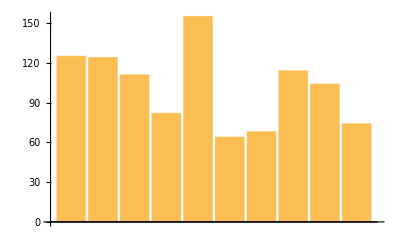

```mathematica
BarBSST=BarChart[BinarySearchSTtotal]
```

### Uppdelning av insättning i BSST

```mathematica
BSSTsearch = {4,6,4,17,9};
BSSTinsertion = {62,50,94,90,101};
N[Mean[BSSTinsertion]]
```

Medel för insättning

79.4

Medel för sökning

```mathematica
N[Mean[BSSTsearch]]
```

8.

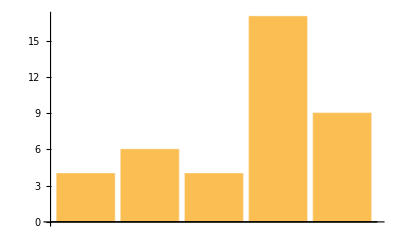

```mathematica
BarChart[BSSTsearch]
```

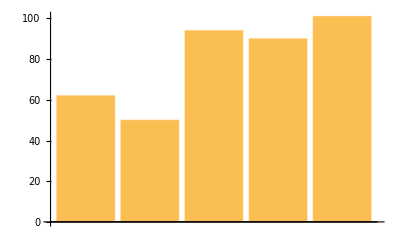

```mathematica
BarChart[BSSTinsertion]
```

## Uppgift 3

```mathematica
BST = {52,98,103,150,96,198,125,65,76,102,127}
```

{52,98,103,150,96,198,125,65,76,102,127}

```mathematica
BSTAverage = N[(52+98+103+150+96+198+125+65+76+102+127)/Length[BST]]
```

108.364

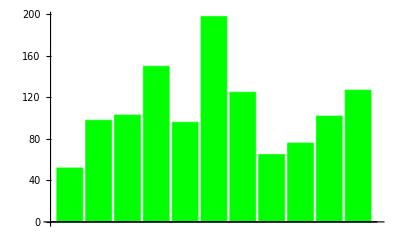

```mathematica
BarBST=BarChart[BST, ChartStyle->{Green}]
```

### Uppdelning av insättning och sökning

```mathematica
BSTsearch = {7,3,8,5,4};
BSTinsertion = {63,50,74,69,88};
```

Medelvärde för insättning

```mathematica
N[Mean[BSTinsertion]]
```

68.8

Medelvärde för sökning

```mathematica
N[Mean[BSTinsertion]]
```

68.8

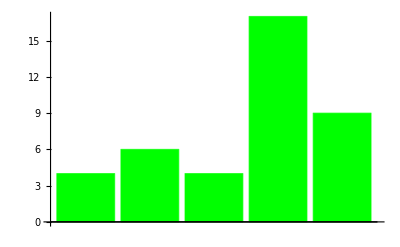

```mathematica
BarChart[BSSTsearch, ChartStyle->{Green}]
```

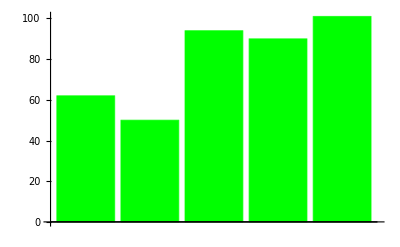

```mathematica
BarChart[BSSTinsertion, ChartStyle->{Green}]
```

## Uppgift 4

Medelvärdet för insättning och sökning i de båda algoritmerna är ganska lika i körningar med 1000 ord. Dessa medelvärden illustreras av nedan graf.

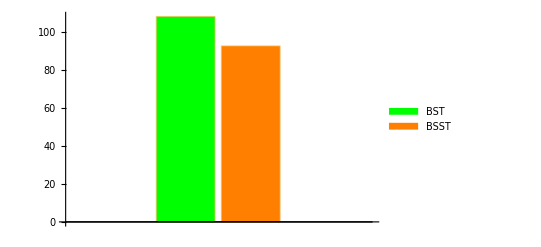

```mathematica
BarChart[{BSTAverage,AverageBinarySearchST},ChartStyle->{Green, Orange},ChartLegends->{"BST","BSST"}]
```

Nedan följer lista över körningar med hela textfilen som innehåller 141633 ord. När datamängderna växer är exekveringstiden nästan hälften så stor för binärt sökträd framför BSST.

```mathematica
BSST14k = {470,845,952,912,948,879,755};
BST14k = {448,449,502,446,536,549,464};
```

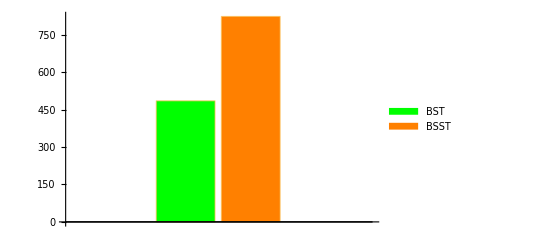

```mathematica
BarChart[{N[Mean[BST14k]],N[Mean[BSST14k]]},ChartStyle->{Green, Orange},ChartLegends->{"BST","BSST"}]
```

Eftersom att BSST har en resize operation vilket är en kostsam process om vi behöver göra flera stycken. Med en initial kapacitet på 1000. Skulle innebära 4 dubblerings operationer för BSST under insättningen. Att ändra den initiala kapaciteten gör inte att det går snabbare. Vid test med denna storlek. I genomsnitt tog det 15% längre tid att använda sig av arrayer i den storleken. Vilket innebär att resize är dyrt, men det ger fortfarande en bättre genomsnittlig exekveringstid vid denna storlek av indata. 

Symboltabellen har dels resizing operation som är kostsam, men samtidigt är dyrare att sätta in element då man alltid måste söka linjärt för att hitta dess plats. Strukturen av binary search tree gör att det blir färre jämförelser om man ska placera ett element “sist”. Detta kan komma att bli en dyrare operation. Här är det själva insättningen som kommer att ta tid. I värsta fall får vi att insättningen på båda algoritmerna kommer att vara n. BST kommer att ha ett bättre resultat i genomsnittligt fall då det blir log(n).

## Uppgift 5

Genom att generera hashkoder för orden i textfilen få vi nedan plot. Det verkar vara ett symetriskt kvadratiskt mönster med flera förekomster mot låga x värden i en linjär horizontell formation.

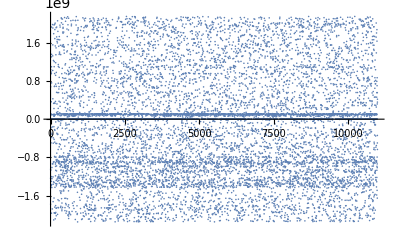

```mathematica
ListPlot[hashCodesForText]
```

om vi istället använder vill använda oss  utav en array som innehåller 10 element får vi en distribution som ser ut som följer

```mathematica
hashDistribution10Elements = {1014,984,1003,991,988,996,1016,1027,1007,988,960};
```

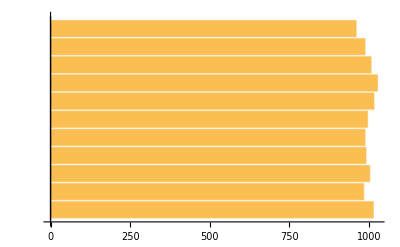

```mathematica
BarChart[hashDistribution10Elements, BarOrigin->Left]
```

```mathematica
hashDistribution100Elements={110,111,87,117,115,113,105,97,118,125,118,110,87,120,124,90,104,113,100,120,122,100,113,103,108,128,104,112,101,114,102,113,96,110,98,114,108,107,111,104,95,109,100,113,113,114,123,104,105,99,104,111,113,110,117,108,113,100,103,119,115,88,114,119,113,108,105,114,114,126,110,111,96,109,115,116,106,112,106,135,109,109,123,112,117,125,87,88,128,98,105,102,106,117,100,113,124,124,119,111};
```

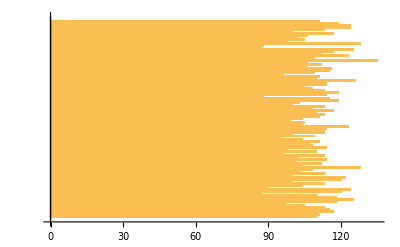

```mathematica
BarChart[hashDistribution100Elements, BarOrigin->Left]
```

## Uppgift 6

## Uppgift 7

```mathematica
hashCodesForText={-1234651544,-1045741142,-1777101295,3194931,676980829,-1423922392,-1066401671,3194937,1032781188,3194940,-318247670,113395410,114704,2588725,95864228,-495230359,3440673,-180226730,-1243007503,983923388,94832060,114717,363648432,3522600,-382981838,-1298713976,-1390596803,951023759,-372020745,1302809999,-1965110538,1926279930,1095696741,-1367708079,-1201129404,758263068,1355436283,2211858,95864205,3178509,65,-1429149039,66,3194994,67,-1009810548,-1243318873,68,69,-292786487,70,71,3506301,73,74,3571837,-1876373405,77,79,-934426595,3178592,-318509741,-161794550,3440742,3522662,3440743,83,84,1978135986,85,86,88,1323847345,1018264811,92734940,1553554629,1906602489,426793262,3194991,2261058,-934426579,97,-1207109523,65635,98,3522646,-1724147368,-1360171378,99,100,-500948416,101,-391190328,102729336,103,-896759068,105,1227016521,-1310281334,93832698,109,110,111,329978820,114801,1787472634,-2105867766,3522631,114,115,116,-157174059,63112118,117,222399799,-891172202,-1648435769,1968600364,-1326370678,-422713779,63193920,1097368044,114821,-1959031876,1202538277,3178685,96634189,682928187,3440805,339514541,114832,76071962,-1959031890,73417974,-217975911,-778874613,953530445,1983772324,689711493,114843,102745729,-1838656823,-480451586,1685021900,1872703292,-233753931,330257163,2195590,-1424430157,3178655,3522693,3522692,-795193304,3522695,2007627546,3424391,93111608,-2083503259,1530764161,-1523884,-1969960407,3522699,3195124,370906846,-938489654,3506418,-1183974998,-911521428,-987494941,916502121,-1807199102,733080443,1179928198,-1068318586,-57787302,-1346228460,-1948988670,3506402,3195115,1346375835,3195116,-508452500,-791998442,65759,1490524168,1911910677,3506388,-850735704,-1860349445,-1281313977,-2019063985,3506395,977992378,-1392464400,686417946,-1352290414,82169,-1860349465,65786,-881112188,-1081721210,-977009467,561438836,141035884,1720133507,1925723085,3440946,-508256077,3195192,-710404959,-1354584503,-292950139,3440953,-861074016,109332372,318116834,-842330914,-1253346210,1625580018,3146023,-891974708,3195178,106841925,1667080769,3146030,106006350,3178799,554360874,-197970671,1594433067,-318264286,110364595,3440915,3195162,3178779,-1990031282,2056829876,-309121858,2212113,94848149,-318264271,-1296944251,94831770,155142145,-1211681031,113313790,1835199523,113313666,3522941,-1684858151,-1237878915,-1845324984,-31424661,3441023,-168872798,-633906311,-865104607,225381439,109266897,751529369,1142326597,1101857022,115029,115028,-1852993317,2343285,3506531,-1207109285,3195240,1664410220,555343939,-901330147,115038,-923137638,1523538863,93193455,-1206601353,-1281854725,-1165870106,630433015,2195782,-876557657,-895939599,-47694784,-1704518898,374724415,680241632,-4931880,1354224091,1082491369,-577741570,873657725,-795012622,1727408002,-889320568,-1336987336,-934803137,-515497922,-795012636,3506511,1403048670,65921,1380111296,129730109,-889320583,98699,-1237895237,3178943,3522981,1658381128,-768109657,3424685,76514581,3441070,1965651122,-1237895252,-1210665356,122177259,110364471,-1496914075,269062575,1925706593,-791146113,-995425022,354817167,-985643798,115115,-532586006,2998687,1544904096,-123782871,65975,-389535362,82359,115131,-1237878900,746335680,-1846456244,-938161749,-82199847,-1528126166,1349456303,-1392988871,70092268,-1071349279,-1820765506,-30048260,-1552686401,65996,-1357943103,110364486,-1268861555,115157,-1062813327,-1154434324,3523048,-962590849,-624731357,2605511,-788934372,2118680494,80774458,98794,3506649,2014820859,-895939724,2100640967,-892499141,696789104,-1662247659,-962590887,-431790152,86983890,-1367511940,-1280069198,-895858535,-1503632284,951024294,3441214,-24511355,-1914236951,-1879208467,-1753180783,-782085264,115219,3441197,111428797,2605629,109757585,624715553,1545035273,2245120,1519786164,1062534515,-330977683,-1006205393,-187877657,-889599790,2245134,2093580004,-1167640502,-1843195892,545153614,98866,-1363530615,866595220,66100,-768536570,1820421817,-1125368107,-1304498169,98878,1982575723,66115,98882,442193944,-1006205373,-9552600,1897755483,1796368725,1920200760,95848442,-1224460984,115276,-1068531200,-795012398,-1085407998,703523772,3555938,1557044890,-1367774164,-1407259064,-1206126004,66137,-427039533,-900560888,1525373104,-1480972831,109413593,-705112156,-836055945,1820421855,-1501403934,-892368721,2556487,66145,110331122,82530,767422430,1518327835,792816933,1444615292,-779709471,1503566841,-1177142338,850391239,-430332880,354670409,83904363,3555933,1379209310,2605640,75532016,-933770714,115312,-854782081,-1137066421,-896071454,112903375,-976943172,-1308920958,2125020371,-837022617,110331118,539320920,-1013349914,110331116,-563241748,-1654399006,967736108,-995326417,2343595,-1911616377,-1436620585,-1849732298,-1366299643,-430201643,97699677,1133429022,-1414158044,98436943,109413398,-888878697,80774724,96061229,-995211718,240454849,-200984944,-969292628,-1084195338,93832961,2605758,1158383506,2046720863,-1422939762,98436988,-1026719633,-1366299605,853651525,-1762175919,-788048992,-1345688218,-82036301,-1654399021,99043158,-123946451,-891320212,80774755,-995867120,-1137525113,-1964947372,397202715,109413437,-947485378,-1790093322,-1408192852,-859353477,99043162,-874346147,-1077756671,-1081279160,951024232,804564285,99469088,109757529,169969911,109757523,2110144287,565093236,-429611848,-1922936957,2998988,99469071,-840495355,-187877841,1406849343,109413485,109757538,109757537,554083307,1884238498,-809579181,327209326,-1115062407,113411123,-1281887900,-1081295489,-117261321,21709747,109413500,1728144888,101647600,-976812346,1428133406,-1192412178,53215274,-1045413193,-1664901180,-1045740894,440916302,-859467826,-393139297,214061005,1022263265,2141060237,-976812331,306581844,94832308,-2005513374,-1240337143,96667352,327209118,-718006764,-765800072,1973237439,487841329,-795012167,-1822732163,-779693393,1557372922,95356549,-1335659704,-1004746960,48923076,-976058627,-925709315,94832278,93832868,-1365463638,931902653,1864936466,996636763,-1498356339,95766152,-2024635281,2110045945,-1790831102,-2075867386,-1986360616,2245473,-753905580,-1380798726,106874133,-493887036,944225033,-284840886,2999138,-109823452,-1408192697,957610569,-1074103135,88737297,835646098,-720202161,2605946,-109823446,-1940336838,-1940336837,-1852747022,192006169,93832956,1080771328,-231526056,481140672,-891319888,56148011,2999134,97322682,94750429,-1396232257,692890160,-839823731,-1969960471,2245469,-661267690,-753233762,950483747,99205,-896071406,-1423054677,3556273,1246054850,240061892,-1272055904,2573224,704211563,109413654,109413649,93832707,1366168313,-661267710,-365614675,465066016,466131026,831697417,99228,101926286,174868978,-1417648098,-1107034717,973732265,624191126,-605480886,110544178,-1997649077,-1179387371,-1045446135,1028554472,-1268779017,-1026686619,-41828822,2058746137,112903447,97699452,1794713942,-1268779025,502308416,-1274742859,-1045446115,-869904491,465065996,1352454952,-575971812,811086820,-1272055919,-897087173,-1411061671,-857075926,1952151455,-1383797171,1985885591,109200715,82891,-1007812571,-930968754,72501148,577397179,366286340,3556327,1466422454,434215475,-234475053,1279872924,-907769293,110544193,95356534,-1304497689,1246054812,-1217186648,1539594266,795847856,-1927770425,1099842154,66533,94094974,514841930,66537,1585274261,-410557331,983759177,795847812,-1131446429,1655054676,66547,110331239,-982448504,-505454044,-1756375884,1551261576,-1075053548,1540677588,69599270,109757064,624238897,-1073740794,-1272401873,2409517,195088297,531635132,99341,-760375645,454237981,2067251000,59131796,97436122,2606130,591963985,-578856602,-70991906,-1304775136,94929335,156781895,-1807790048,-445406894,-1274351573,98533882,-209914023,93503927,1275971624,-482334874,63408097,98615751,109413026,93110692,109773475,1019213974,82991,82995,2245648,-1349309530,-1383716431,-1074103359,1018214540,546645162,-63342472,-1866984197,-814347469,-1383716416,466165646,-241257003,-795274028,-1726194350,83025,1350079528,98615731,-1419464905,-838923862,98615734,-840447568,99467700,3556460,1272352653,65472441,66657,430005698,-1146830912,1022441624,109757152,108511772,756705649,-995409728,79233237,109413096,1415385139,822179182,-442048043,-880816373,109757182,-926675790,501143977,-1383290379,844740128,1399920395,-795274014,111428312,-1335249899,99455,651403948,99456,99458,-2097084540,1351177228,70320310,1575868773,2061581929,99464,-937587567,1422135369,2064187269,-809546959,-677506287,97304899,83088,102744716,1186644526,-821720176,1118799417,103891625,1652745754,-1935308739,96895327,915501581,1244991146,756705669,94011707,1617355975,109773353,1968370160,-1419464768,3556498,-853259901,-526130165,109773344,2143927138,98615627,-26658110,1293601206,109773351,94011702,-905834836,912634571,102728365,797764409,97436022,-1106740560,466509684,1763470759,-308532960,83132,949550119,774367975,3032303,83138,797764424,-977092345,3015911,1276119258,-1811099450,1526144572,795847588,-1331727278,-892482046,-1992012396,99172665,106431112,-903459084,106857100,3327206,-1971908959,950484093,3327208,-1331727292,-1528897533,-26658124,-1352389753,-1106363674,1853762198,-606937285,-2147416853,98615564,1332808583,3015894,109757041,-353538538,1770843504,102204139,98615580,2067300293,-1335774049,-1247940452,1102578873,103334698,805827841,-934965949,-675228979,1912796943,1884829013,110330781,626483269,43747208,-339185956,-1073068772,-265013972,1625957874,3327275,-341152080,3556653,106677056,97616077,-554312725,-1335773825,103449397,1064385104,902852849,-1266503261,1223839184,-854095820,3343637,-892481564,93618367,-1178551060,2082099,-1077740819,-1313803136,-1211583751,-567321830,-733294212,1034860696,95027346,-795011675,570418373,99644,-561521736,-892481550,1070217866,-1067367135,-495130819,99651,110330838,916452313,-1367774402,328603356,-1634526243,446930930,480401905,102204227,-891990144,-1371100399,1116309457,141692202,105186077,327144998,3032436,94929138,95994082,109757398,102204232,-759326750,1289636286,-1415139642,-677145915,-1694409109,1256804229,-409246985,292983835,-788048780,109413361,-874443115,-897347594,83323,273257783,2573735,3343799,116103,-1867885268,3343801,1856465709,1567250656,-1377900459,2360751,83340,102974381,110789386,-1963700378,109773592,1510776730,116118,379114255,1193968317,-690482368,98615419,-1176880063,-1352291591,3327407,83356,92913686,112902938,94928904,1463587485,2049469,3327377,1934014179,-234326098,-1480760809,99755,90259659,470604199,-891990146,1535319599,-578021343,94011444,-1569675328,109757243,-2097084752,-199315028,-78250266,950484242,-765470743,2688405,-1377900445,613769512,109757257,104694772,-963853498,-26657886,-658498292,-1495030994,109757253,3016191,1136969238,-468311612,-1052736365,77381960,-803105292,-1217006942,-2084878740,3016183,-763766880,79151470,-540026348,3065333,-1106478128,90259644,3343854,103662578,1429835993,1202553421,103662540,-1390515972,-1252986702,110363510,-934933088,585295621,-612688237,2119498684,-874443254,878719374,979894153,499324979,109757306,585295635,1355322681,-1405539896,-1955869026,99828,99830,-795224735,-20153545,-874443238,81068331,-2020605330,-926053069,-881046147,1090717442,-1184170135,246302888,-1455984848,-1170621392,2082324,1846175745,-896594812,3065381,-567142338,110624917,348607176,695005053,-1217482369,3016252,-494705513,-1455984863,938160637,3032632,1913009182,2688560,3016245,-551298755,-1829579540,93930425,2094529267,-494705498,-2033975059,-1847355447,-204868125,83500,-1319569547,-1414877817,-222710633,1707484136,1542036953,915484836,-697905071,-505452569,-752233200,9946798,109609139,1441846221,3343885,2057747685,-1322977439,1649517590,-787687612,127156702,3327612,-348803718,-838416311,-522328435,1124091217,844215300,-1924019450,12273379,670343596,1937372451,-261851592,1525161141,784296160,67169,-916533444,-1795452264,-94569416,3540562,-125780248,3343967,3540569,-551298740,2110045108,80085687,99952,-612557553,-1184809193,1957458650,1409815167,-1001078227,-1969648411,109314299,-1335150869,103661741,92750597,102744221,1316866302,-1774579522,-788638085,-189271503,108282108,-2000515510,605184667,109330445,-1795452302,-536697202,-1258687884,1601542650,110624778,2361014,-1338968413,1925739612,-1804266784,3016376,-858371519,-1134986559,109641744,3655341,1270893914,3016370,1546230455,83614,-1605867799,-968916834,-1824320030,-1410339510,-431709983,810710772,109314082,-906342564,-931148072,-545220312,1960030843,3327647,1043855514,-684600932,-1711317167,777693428,95470367,293427148,1946432181,-1870801202,810710758,68567713,-898708266,-565470989,-619520597,2573982,-759491578,-898708272,927183356,102203604,1264422296,-1049376843,3327733,3344116,1714725107,-1642374948,2606829,-1317292107,109641799,93029210,92668757,-1354814997,570402602,955366950,-840643789,3016435,3573480,-1361631224,3344108,50955753,1506942774,1349785232,3540691,93029230,-1167197045,-1897183229,1732829601,-1628055521,-2089450081,3016384,467213623,-52151785,-1976136507,-1011284662,-1894004241,3344071,67339003,3540684,941899480,3344077,-597927262,3540681,3016401,-1448923481,395923612,111821228,150327294,-207588180,-650043828,3327779,1378178359,-934654119,3327780,77382538,-1894004733,-1383716193,1502322321,65078524,3655444,3655443,3655441,80004067,-2086861638,3327765,-1840949907,150687699,-1367529129,-1893496819,103334151,-1785834817,1196982379,957939245,2035990113,3655435,3655434,-874820379,-892482061,-1897199148,3327858,2098788952,-1249512767,980073773,466885788,-227642074,-906277200,61703393,-892072551,-1522589070,109314516,-1423004545,-204524388,1447252246,100182,-919662985,100184,1480875803,3327826,-934326481,100197,1529584707,173247800,2052357439,-918548948,-2140027107,-1653794304,-1284885497,-1206091918,1469583606,-1259490430,-2030599806,1115243790,-1289358244,3540810,-1901786663,2574170,-1294158500,3655604,-764553752,-1379227070,-1275743108,-1545477013,3573671,-1795452056,1029110467,-1394332815,-590996656,-1868048592,3344297,-1335429178,109642024,-2020327373,2052636144,-919662970,-1564908270,-1595971726,1505041947,2541448,-785557886,67504,1584683461,-1338968189,-1011416060,-547120939,109642032,-874427304,511531462,109314361,-1344133028,-602416169,65078309,1341032489,-945995691,-891974371,-787736891,-1732042999,-1357518626,-902197771,1874684019,-1893496595,215304986,1118815609,109642078,-334648364,79889178,3098612,976535017,-213142378,82658098,-1427624695,-1101891152,-439770579,98615813,-808630229,109642094,-646160747,2017198032,1957573442,-1672520799,83952,-1357518620,-1969648277,1955410815,-892072665,-840447469,1877780505,1117717865,-1197605014,-1628055283,2115664355,-435297802,83965,-706866653,1481625679,1984986705,99044836,3704893,-1288799445,-911343192,-1896986903,93228423,1875666886,99044842,-1381030494,-858536765,-1377688078,-1339115460,-1629776180,1917942344,-1423908039,792536868,3377194,3377192,2092627105,97193429,-322542376,452301547,-342498422,-938491858,1636198820,-154337564,-1911224770,551676106,-995865464,1800495997,351608024,2054419011,-1897101602,2098,3540994,-1272054757,-2053648978,83545287,112217741,543811625,497898989,-1864820583,867089388,-2127558285,2115,2119,-694624545,102846057,-804530109,-1800037122,2123,-288446843,2124,2125,-1812800580,84049,-184271531,2130,2131,2136,1951480841,-1198116662,-1419320520,-1394187080,945975357,-1408113552,-1059534663,2147,67682,102846020,1481625641,109776621,-2083370054,-1323665039,1095813435,3377247,-1900214577,-1861789325,-1206800281,2167,1645963884,-905723276,-1439129024,66292618,-1381030446,-925138779,100479,1341065070,757376421,1540559697,105008833,382967383,-1294648750,1080543470,-765289749,1006826633,2188,-1577621126,1504891197,-895679987,-1039267172,102846135,344792090,-282957894,957067667,109415964,-1326401430,824998326,-291330497,97193300,1160678797,-1358878811,3377302,112102920,109399597,105664230,73075953,2219,1888679993,1711222099,-1021473869,-1313638115,2009169775,-1131301855,103157406,97521001,-1089636428,1855940134,1725984347,-1224458312,-836041066,-47057524,-1039267152,-314497661,2243,-1563727352,109399617,-1412832500,1857791614,-889322955,-1385863765,2058334817,1982693091,1538954101,-681304139,98127112,-1376180952,2014441667,-182043148,102977264,-1298662846,-1206128436,-1480249571,102977274,100571,1560614366,102977279,3524840,1394924538,97619214,116958,-2025861154,-1361631690,1527960566,-1261192138,2098787826,1849845423,-2008465223,105008818,-567322914,1097468315,-1697230300,-896073117,1920121479,-977121996,-1113836182,-170934986,-2000011213,-1392466439,79219778,101306099,-816822357,109399674,2068984402,-1269727920,110628761,1120930770,-925285926,1615358283,-1367775363,2312,110727062,104714029,-1504825505,67856,-633580755,110628746,-1050408836,2329,-1052669861,93998208,-1527157278,-211518849,2333,2333,-1193315904,2336,2337,67964206,109399969,1999027714,2341,1987346258,-667299553,1547179295,2343,2346,2347,97619197,2349,2351,-1357535707,-1237876985,84274,950497682,1436294315,-1237876978,111972240,2365,1223328215,2373,-1443192654,-903576723,-784050163,2378,1137494663,2379,3049826,-2004500021,-787736481,93113560,985199596,100692,-931102249,92933341,690872437,860813844,109400031,-928497163,-1663019586,1246249771,84327,-1081084186,67947,-708600658,109400042,-2008465092,321477214,-17500273,97520721,-129355320,109399814,1807622715,84359,-816822569,-1077561780,-907689876,-1854236432,797730310,-327916034,104583095,110628630,-919977819,2080421264,224576755,-1026733217,-1274446437,2453,-1215332838,-1380801500,735928901,919650121,84379,102977465,104075176,-2094363978,-123948800,1500369139,2467,1728245414,93621297,-1497370855,-2021994788,113315686,1921547055,-522589826,-1293665460,109399852,173474814,141050310,-1417469396,1920367559,113020685,-498979853,81087844,765912085,84405,2484,110628654,520050504,2488,-193544753,-1537249818,-622800034,109399876,2497,1616767390,2501,1249149873,-1663986409,357555337,190874279,-1323665200,2508,512825181,2394603,1550783935,98634800,-162005115,109645658,-2114664415,2519,-2132162255,2112320571,-1965178111,-934592106,567961658,2529,2531,-717153114,1090717924,-1323763471,-1062713022,1052964649,-991851251,809204182,106762162,-1402346106,-707929027,84467,2551,63343153,-1600034474,2551,94637148,2553,264521277,985871161,-1049376625,97618991,2559,-891207455,-865597848,-1658366172,550660817,2563,94850990,1627679503,-1317192846,-1412832805,-1076693567,157467510,2011004359,-24841058,-780575902,1091832591,-1854383260,-1686007396,112905370,1516785737,-934624660,-1935718728,-810990207,-1102433184,1352637108,688005934,108399706,84524,-2127738110,-134578731,100913,112905355,921353432,-795125073,108629068,-26053564,-179191961,-865597868,-608431741,-40912946,97308557,-1409474114,1379964934,-686187169,-851179773,96653192,-648604899,79154919,-553609903,408736270,-1241530452,1931213133,-965882821,-2078863808,497375231,-816904939,-1320944872,-69865079,665251320,93507570,-516183207,1910897543,-1059468613,-1211515478,-2107914178,-1102433235,93818879,3377752,2030269294,2104194820,3541575,2067296585,997290243,174981147,958018413,2683,1018214091,1869063452,-1324074129,2684,3541578,79646401,-1858512057,76517104,-962179879,-1678503541,166036325,2689,95997754,-921943160,3148469,1091406727,95997746,-1285572140,801006896,-290659267,-1010022050,113101865,-1010579113,-2021995026,2708,-580429838,1514819804,-1854383121,3213995,-621801366,2715,314972250,81088075,-1194823082,2719,1971879720,1667852744,85299126,-891125689,103894167,-1418141217,2054222044,175554779,2198156,-125341131,2739,1378982018,1521258520,102845591,-1654745112,-1458674760,-1008826007,1746772644,2745,1093847944,2747,-1274708295,3377907,-1022637617,-891535336,-1851942053,853620774,-1883798148,-891207635,-1731259873,-798549323,665251189,213681768,1410571975,-1089096241,753641009,-613887565,-1892432402,394992982,1556125213,2018521742,3377875,1478300413,3492567,98619139,-564570950,3492561,117481,-1795678704,-1115211921,-1953496712,117480,1623812640,1979858153,3181277,117487,2798,3181279,117486,448598098,2801,458002878,648162385,-1592398874,-1857627214,2808,-1703702389,-787751952,-354983892,2814,1795826165,2816,3443508,-1858479558,-1798463543,-1268695193,658336826,-353951250,110136729,-1335723160,-9915293,-807058197,645705074,1956052889,101139,-1325958171,310319468,-2082649906,101143,-315054546,109776284,101145,-344579988,110136714,-1179159893,3443497,-650472929,-1325958191,-1120700903,1839654540,2860,79777773,-1096862286,1270120576,345710511,2870,-1106201306,-1854776764,97799906,-1282033502,1453055394,-1932326934,3541773,-541207418,1964277295,597256354,-934427789,-2082649886,688087612,-1405688055,-201244863,364273398,-1335395545,-1524453790,109776329,65767598,3148661,-392125465,97324676,-682140642,-685286290,106663185,-1377753426,3165055,-1791074706,699491040,-1414881026,117588,2427773,105827604,-596617430,-547482624,-226133542,-948827118,3181392,3181394,117606,860813349,-743417636,-1290684291,98619021,-482138066,70209345,3492699,1182518549,802317473,80089010,-1095191091,-490575430,3492685,-1392826494,109432316,111873495,68476,3181391,-85626470,109776372,553069428,101253,2080913292,-1409161339,69062552,101254,3083175,530584619,-730488839,-1421565752,-1883798472,-1408178273,103157172,-1403295794,-1781719464,-921943398,1018214183,-788817054,101272,-1684221946,-172343772,-891993739,3492756,-995602677,2427779,1194839199,-45599008,960328341,3541919,-1010579351,1280837618,3443608,100355670,-891993733,-1314244092,-810515425,-1003761788,-1010579337,-679437259,-1106037339,3214214,-1306084975,-1439129201,1345559435,110546223,105745905,1441652304,109792566,428085817,117694,547400545,3165170,1171738130,-409490351,798106714,117704,97193474,1400608945,-934624384,3083236,-1339114499,117717,798106694,-1081494434,1400608931,591505563,3083251,117724,81891134,3083215,-1377688064,117730,-112905566,-1323779342,2198474,1437916763,-1001844808,841365970,236799467,84982,84982,-1832593092,-353951458,112217419,-1115392385,-1335395429,-1289044182,80218313,-995424086,109562502,2493477,-2145760226,3165239,205422649,78842043,112396986,65376232,-1096977774,-1106742777,101393,109496982,-924433161,-1126043405,3214370,101397,-1211647009,1393975055,3492908,-1034760629,-1424120063,80218325,3492904,106940994,2493496,-1226589444,-1325957929,3542038,-1896693038,3542037,3181587,1315390019,-903068151,-1321239270,3111,1900805475,-1825546470,408818804,3115,68650,3116,3117,1916042777,-1268778895,-1289044198,106941038,-20843792,3148801,3122,3123,-724952839,699573633,-173852268,-859717383,3128,349788387,-1519228600,-1268778909,-656304931,1431984486,3214351,3139,106940956,827096331,-1422235790,-926251903,112216829,-2049701477,-988477094,573943396,-891484533,3148902,3159,-2023617739,450598530,2043196817,-970454411,755933523,68703,3148910,109202141,-31690173,1700882750,113134305,68704,1642196352,-631138813,1503532540,68706,-1361632588,2493506,-833093059,-328703986,-319987574,658336602,-1240155524,787407493,141050885,-2083958873,3148894,101491,-677618706,-940242042,-414766285,-792929080,-677618712,-985167565,-2127770277,-2006285294,112397001,2097181052,111430360,-1266403079,503107969,3214412,-2078078883,3201,-1003272011,109251077,2133259182,-779297530,-1613589672,3211,3148988,117901,-1371921740,-1651322596,1589023266,2112549247,-1166395665,117910,-190744522,3493026,117915,-1291452514,117916,104696483,-1790649893,113101341,104696477,3235,987674237,946730190,3240,-1386339852,1214416073,2182284,3246,-2050799252,-1002075915,104712844,-608397555,-1081314499,106662638,-129813258,2706590,3165322,68795,-892483983,101564,-1560186945,-982480434,-1255556629,102976225,110234193,1559810111,101577,-1736108978,1650323088,545156275,951530617,-731293509,-678782119,3083516,-1950496919,3493088,92899676,3443937,109496913,2039313751,-1331463047,3493102,99469622,-566947096,951530601,-812334224,-874821825,3304,-2030335470,838860052,742908075,842481371,1308918516,38391480,-1148684423,3148994,3148996,1010921653,2428114,97798435,521655279,3321,-349378602,3165387,108399245,-1423874083,3325,-901150903,995096143,-979220317,-1109987113,3329,-985774019,-241763182,113101755,2039313547,268174074,3335,-1331462737,1725901778,1613770046,-2027353562,2028533240,3149088,866401973,1172818164,3149094,3116345,-1310311169,550874574,1542133488,99617003,3357,-1597461016,-594112074,-1102761116,68899,101667,3365,313843601,761962572,159466665,3370,-1081298266,3371,1839915137,3493150,1917157230,1505268886,-649620375,-1948580107,-985757682,-881080757,-1097501786,1973237934,-1102433415,735504098,-566947070,691430401,3165449,-710535009,-1392975417,-793141767,445732819,851230718,-1109790565,-691594353,-29707408,-1668329019,1687874001,73828649,-518198189,-1744775855,-1888419293,3083640,1979923290,1611558231,-634267800,77974012,-1200507606,-2096804258,776561429,-1392713311,92621016,1550569781,-823606346,1147603204,670853784,892123208,85351,3296597,1197722116,-891238517,-51678842,1106332828,3149150,790307445,3296579,-985774004,583380919,395188989,-1793484691,35540843,95848643,-2122658801,3445,-782181354,-437737322,3456,101763,-425612509,-985773895,1480857037,1487443233,-210452739,113101617,-906279820,-1416550882,3558823,-1281671671,865631755,1752770026,-988477312,109497107,118167,3558817,-1333183202,3480,-1097452790,-1035284522,-982480658,951530772,1979857829,3083655,2100619,-975763332,1020670333,3500,-765796364,-436393907,96667762,166757441,-122522368,3083677,159466549,95848451,3165573,-1819533766,1979857844,104991738,1555222794,1161234575,-795009753,-536826437,3493257,2089283897,-1814094305,3198448,3521,1431345301,-1879145925,-1766368400,553970892,-1131138723,215679250,103910395,-1418828127,3198432,-790192845,1544786374,3543,-362993782,1097075900,3545,-2029647140,-1993784077,3198444,3198446,792748702,-934443629,-631548027,3551,2147316258,-1380802478,3555,113101662,-895760513,3561,-433984565,787407618,-1354571089,1134120567,-810024361,-795189909,1843257390,-388094675,-1131138708,-1091276019,-1310311393,3296718,2100457676,-1985182638,-996767081,-2080928267,916551842,1080413792,-1052618937,1509677052,-253919531,-1869930878,-1208141321,-1041657885,-22859608,-1269286317,-659450179,842939439,-248873159,-1141148177,-1154845378,-12963537,-2140549505,-925677884,2004531554,2024011449,-1396170030,572451845,-940914191,-162006966,-934918565,3558952,63294938,94636932,-12963557,-1452611765,3558932,293429086,-104204307,1090490074,151619372,3558940,372414488,-252838201,3558941,-1899511576,3526149,851344526,3635,-795140435,-2013264328,-1326154035,-1010250254,506253335,373266436,-1380801655,1461590366,-983659745,1547276920,537538120,-1205602719,1093046117,93621200,3526257,-315858070,-216629921,-527208743,2043017103,872643151,1000846827,3526264,3526267,3526266,-1818419758,-674506343,3666,467228042,-1409195435,1703832538,182617274,3676,-1353359095,96619420,93014996,-178324674,1170475940,2100753238,-2121543702,1980381289,-902265764,-651487409,565719004,-1676111234,109627616,-1357520516,-1081429533,-1897185151,295493622,80890552,3198556,-1971977190,-660072763,92670952,-1357520518,138429999,1236617178,-1271629221,-902265784,1058222434,1039348608,3526211,-475304484,-1357520532,-1271629235,840416366,3705,-620145293,1425955460,3707,-369449087,-1818419738,-253739362,708830399,902347594,101304458,1302823715,-1756636722,723019166,886864475,1998813611,2088104700,108873975,108873974,-1388780619,3727,-1097519099,487510942,-1708550981,-1008677517,-1937423856,108873960,-87018426,-1039102840,3737,-1416125171,3739,549547610,3742,483873353,-794960324,408671993,-137741975,111593474,94227256,-1791517806,-840203444,3559070,1486984713,554233765,3759,-1901789174,3559065,1424906817,1926872182,1449826522,-1791517821,3526272,-1086574198,97618791,-1670081853,-1259832737,3296907,3296904,-138151554,1197722078,-1266091467,738943668,335076664,1846386895,1070674195,672753371,2142925177,738943683,98634538,2031351775,102093,-1177422051,343153337,3790,-1142049501,-1768777635,1911062328,-1751869120,-187237885,1978596153,489051121,109267028,-587214297,285187621,102111,1038086913,-903068430,-794960318,-1061548456,-899644285,-1273775369,-1685318295,110233717,1080413836,-1224361489,-1626533384,-1335656807,-1543869177,1027142599,-1349066601,109562243,3198773,-61689001,-481711025,2543392,1341505778,635054813,-1354571704,-1075629847,-1323778541,3852,-1392319985,-865287327,-475976532,1967372881,-721167849,110250375,-63016151,-1335656583,1979775258,106940740,-1899740700,-237633804,-216892368,104581405,-2140549297,1428183562,1807312019,-1537168565,2008578197,-520049106,-1272808692,1468962977,66915532,219120190,-1314636143,-2058794369,-1282179931,69430,96946943,-321788952,2576157,97618667,2143957238,1637183144,354359901,1900953099,109627853,433919643,105007365,-1571853048,18648667,259244095,110545371,994604056,-1854677466,102230,-1354571749,452728229,-905689763,-1396235364,106858757,2141401336,79137751,-930658329,1037791929,-1291322268,2119627061,-36212033,-403412835,2029746065,-1355030447,-1852006665,3559258,-1671097591,93997814,92605161,1429543514,2543433,652093873,3198785,-1193232495,-677734168,95472323,840416612,-1024864870,-1074040690,-1307116191,-662464524,96651962,630549229,338418514,3526476,-792043595,95849015,-1593970820,-1679829923,874544034,109627663,-1657679178,-227656217,-161826349,978433498,-2140762133,1114000873,991966384,-1881751481,795549946,-1722362172,-1224574831,-333143113,1945697379,-1136184345,-1030632143,-833601039,106940924,1126681732,1558614853,-726803703,598862868,934049803,1549505523,-365877863,-2123919667,-1149144019,3526552,1366466271,1810572356,1742465131,2035631,-603335752,874544019,2064331967,1755555605,545681214,936933474,1715644920,3526536,-1149144004,107940306,161515038,-1935391973,3198960,-1274266676,-220463842,-934787187,-1289126673,109578560,109250890,550252294,102348,3198974,-832732781,1812898782,949122880,531959905,-502256185,1130843327,-1897135820,-1278411755,-1084968817,-1635806815,-1965718262,3198959,-903068212,2057418048,94849606,-1897135858,-2146725905,-1278411735,-1377508863,510480773,109562223,-1268958287,-1785619843,-1183762788,-2108650080,-2034316977,1125190883,-1953479580,109496703,124897421,-1183762804,570420737,80778450,1470990254,-1883283526,-1808513998,60887977,-864330637,-350553325,1563544891,-2129932032,395085697,115168979,1355153608,-1969890661,-806101020,-907765250,-817651879,512462487,1200773006,-383862466,975628804,3559442,695351639,-1375584731,-1897144628,828367224,-391235450,-1509591511,-1335156666,-2140467131,-1092964619,7082076,-1081299012,1731786507,3526662,878060642,3362829,-1097060702,-902473098,-1219467501,1544916048,-842474098,115168923,-924739417,-948824267,-168729162,-1073893451,840442449,-791707519,840442455,795787041,-1595805517,504368707,-1102877155,-1354825888,-341328904,1599180595,-1491142788,3526737,-268599397,-1301388798,-919955129,-891528531,112088799,109795064,-2054826506,-418302110,987507365,891970896,3002454,-306987569,115168928,3657802,-1137578929,1312628413,1094603199,2032888233,955164778,-934979389,-409241840,109860359,102540,920708718,891921848,-27005199,-667219793,-1886249209,1815493792,-611185915,1064382443,-2040113412,93197586,3002509,-1062842361,3313815,3362964,-1347961088,69801,856777658,-462703424,109532714,-1209424039,110532135,1738667792,110122531,80204913,-1867169789,1846738596,1475610435,-525864929,856777644,211442725,-600044291,-1450739386,-677443748,1738733414,115168792,-1167316311,-1405846276,357647769,-852877853,37999241,-724728832,62509943,1415414930,1335484246,-677460152,339510492,-834674977,930490259,-1907941713,-778927750,1366180231,729267099,-372688583,1841495347,110122594,2118594226,-1403061077,739065080,3313866,-865887077,-1412351189,529731438,-982936170,930817657,104585017,-1993975774,292831344,2031511570,-518098920,2314539,-1349058913,-242327420,-1347780959,1432421485,113399759,1185224616,-778846050,2126852043,2116726586,-1978541310,1431766083,-461589144,-79713752,-1352401285,3035446,-778846065,113399775,1126765110,2089299351,-1651045240,-603484889,-581514121,775634713,1412695312,-1221253615,-1650864961,358728774,-1322278904,-1764325378,1671672458,-993356319,-988474306,-1428096051,-1661628965,797998783,696940731,-287997977,2053811033,1800551012,2053811027,1997628973,3035410,1557237228,3035411,811393379,-793443958,-1381041007,-1109939049,2249058,957950040,102720,107943726,1265392174,3641717,782958569,-1241570116,107943722,-931194567,-1510951751,2026858886,-17076304,-542011651,2121740088,1957570017,-2042161386,-1052618729,-1857224683,3641709,-492014601,952215965,-1312563043,-1428096065,-455920244,2134666844,-2092035537,3314000,-2044635325,-1639854302,1260427843,1136956064,264085209,795311618,-115742593,3314010,-2047486819,68818295,-539210063,2054073089,-1733326369,546173438,104585032,-1436108013,-771325069,409389329,-314573752,95589576,-1298275357,-601830049,671938931,3559862,-216407397,-734345794,-1414841810,-1505265727,-1983424434,-647558932,-793493185,-1550945790,109795078,1794685801,98440268,3641764,-1965778112,-773668745,-2134929110,739065240,1313021909,941107598,80778567,1360756867,-816439603,109582100,1038232703,1819065842,-372017037,-1891246364,-222715109,3625364,284885341,-1110266764,-525602547,-1528351410,-1926767475,93508665,-1893556599,601485940,-341329399,-1822358833,110729014,1003907686,3002781,2511254,114464611,989834062,1943921253,3002775,-1970447562,110778151,70081,-1142691289,1094504697,1471661681,-897918020,-234331185,-1845460021,111433583,-62296697,1585581907,-896607396,-976940010,432834584,-1193236171,3559907,3035641,-1354776856,96965648,3314155,-2072685140,3314156,2249154,1585581922,-4379043,3035599,-1853194133,-422349006,3559892,1611297262,113399591,2030463201,1212963237,467044927,3314136,1359708385,-1973707855,1441924099,1763211497,951068996,1576094725,-1351975268,1599295146,-839050233,3641802,3641801,-613004664,658405057,3314125,-1281826406,1138758115,103666725,706951208,-1351975578,1987142781,-1237654474,-1185207466,70161,-423889751,1526286573,-1217174170,-1790851244,-1106203642,-1989207180,-860496215,-874702399,1233099618,-1291329255,1905419148,706951170,835560430,-2116856848,1784199293,3641872,-605484594,-1963370285,-554545959,-1580059655,-1184224424,-1250252984,409881178,-977119238,1728361789,3363337,-1360216880,3035667,95852424,94623715,1235459042,-376652851,-134257219,2249313,-1215109679,1566314264,-131110296,1149671116,3641980,94935011,927851777,94623726,-938042789,-2143202801,335430064,-1024946010,1848048758,97621890,-565752812,-1511426123,3002992,801865110,807543420,1043442770,-234266516,-423807784,-728054017,1085444827,-1253169372,573943903,-2102177570,273089066,-356910890,94623703,-1246697532,845881374,1626256024,-1897669480,-395249140,96901048,-318668928,3560117,2462369,-1407254886,98539350,1829060492,103051,-906273929,-1234885400,67770010,3642021,3314342,-2119036122,1302683440,-921822312,675101355,-874702523,3560110,103067,1922965508,1216322277,-1405845842,103066,3314345,1094603680,-1324932199,-2137386437,103072,-902473578,3314326,651457648,3642001,-791592329,93509434,-921822297,-791592328,-1353531912,1538951440,-2136059388,-903145317,-1174656180,3641990,1210243731,3641989,938321246,-1361527701,-2042948466,-2055153865,-1070361980,94623515,67114680,3641995,-234430277,-938091864,-1720759377,675691142,-1884349074,1495124958,193714509,86729,-2141384043,235297998,-1306074900,338347745,94017366,1434715976,1076925181,94852970,3642105,-1621979774,-791821796,-677771959,1977870135,1800550788,3117816,1552895574,-1978345266,666760551,1148737187,-892381166,3625706,96278371,658404833,1671426428,119527,119528,-1817706175,-388515267,658404819,112890954,92903288,112890955,-1281711765,-1354842676,-196794697,39243940,-1163499437,-1604554070,70391,651179048,-2078075175,3560141,593228192,3035859,499142463,1844002538,886138834,-810705746,1312578874,99047136,2015914799,194812053,-1331911790,3560248,69490486,103189,-1548816198,103194,105600343,1555582887,-899868292,3314449,-1224334299,-2081386285,109860266,1623536620,69916416,-1854717351,-866279567,-33870134,-944810854,-1176638744,3560192,65376466,1226562082,-602681556,1483442986,-332431507,1849965830,-151935566,405162850,-1062890527,1846639957,3314548,-1077613426,-804109473,64065695,853189002,3642212,-1361052279,2364284,109549020,1963992654,-1289822143,103716175,-1307827859,94623425,-1106662038,94623429,1099846370,213704652,109860349,-537686911,109860350,-119247977,86904,70520,-1253087691,567669423,-1970447886,109548807,-196319283,103299,86917,-1392885889,86919,1787951385,103308,2108288548,688421510,1084068621,103315,103314,648803644,3019702,1189352828,2129882474,3019700,-554545816,647902466,83760994,86942,1225251480,-1423296331,-606762891,-1539852395,94934538,156064494,-1096913606,1240881744,86952,-490589845,-339724183,926934164,1776482889,293372625,534252662,834544145,-894674659,-178739479,-6607830,110777640,1943920746,1268455463,1638117918,2047371727,1099829830,-168876506,1818558377,106845584,-228695663,547369840,361006677,567390720,-29479443,-1963501277,-896509628,-1972823617,-2090151747,-854794539,-1587547516,-303628742,1053158683,660387005,1556926254,-1266096278,-1048898919,1097519758,-1502513769,2462668,1038429708,-1818460043,-391201982,1239767560,3347395,3347397,-793050291,-823812845,3347403,-702675482,-1525319953,847815027,-1278009298,1897390825,94623324,-1316444792,271418413,-865118097,-1271816144,3019820,2708525,2039868817,-1712583196,-1143410736,2708512,196353982,-1538478016,-1131566974,1897391366,36476472,550253784,1241816592,790035214,-637760026,-1271816150,-891986231,119839,3019824,-909894182,-322668326,-256088940,-1422950650,-1292179757,-431738258,336576548,94851467,-1073878064,2692121,1897260325,894099834,-1591577327,95457671,969879031,98128353,95457672,-2067230478,103483,1728557884,94097831,3019794,103338600,-1807990659,-1073910849,-191012642,1675261854,-903324049,938156961,-1102566908,103501,-840246874,-823764309,366313883,570406320,103504,3052618,-2069868345,2097113237,-373408302,1912530322,-1516260877,87149,775699024,93819384,940354659,-1667086126,452152962,702266792,-1412808770,-697646562,3347527,94425557,-2073194469,-336625770,-874438758,87164,1326898025,1216568572,-1423835298,1109137052,-218503555,-1984635600,-564852014,-1782234803,1346159796,-309216997,-1106744699,1912251767,-325683194,704150892,-1331911670,876568744,1346159782,108401386,891855285,-1857632794,70825,94851343,882745396,-1160565121,2987136,-816227352,-1628403132,-1349551301,-1181356768,1977999699,-793000954,-1956356135,5788903,93819220,1116313165,-1072065315,2692334,-1272045338,-477120697,-1804189507,-1824110700,-1374176572,-1548945544,561739183,1718137520,-1309055712,-893952402,-896950701,852567563,2032201211,-748369991,-1105925430,-896950697,-1039690024,-1386153537,-17159643,72650932,-823698937,-1091622389,1780121331,-503761646,-1131353987,3003587,1758903334,69062892,305465030,2035477926,-1365345685,103672,1244274388,481134674,103680,-1396196922,3118380,103687,-1304451272,1925736384,-1382762340,87307,-1073927447,128307888,-1422950858,103338801,1871837834,97439982,3020043,-1661941290,-454905403,1998250547,465391254,3020035,-904257739,109597626,-1898423318,-1420591520,97439997,62264962,1222352365,1080382802,73404759,3003674,120623625,1114134356,-903340183,-111432673,-995880479,87369,78959100,1550584101,-1221270913,-1773387001,-965881055,96505999,48781243,194617039,-678739246,497518846,1893672320,1936401935,94851265,-868034268,3020105,-891985998,-1220763050,110547964,103666502,1043442522,-1871018730,-1048439561,2987354,-1048439560,699170007,-944680244,-2132535964,94834726,-1268784675,1572079670,-2049732521,-685260126,2692513,-1992074038,-874439061,561886454,1279875525,94851114,93818904,-734821982,3052989,-1211129254,1855372047,-1299732710,-1547717086,-1138529858,2364857,-838280297,373556196,784989032,1955373352,-896688344,95588373,1448018920,1305942142,2084481431,-766441477,109761319,-600094315,-1027106953,-1162547452,-1268784659,-43947821,-1268784661,-900931593,114922338,-318277445,-896950473,69915028,1126995602,-1064282834,-903929952,-1289345308,-891986153,-1392707265,240425879,156916889,67244487,68981210,3020260,-1078121871,-1790869364,1380091794,540734954,1772010570,177495873,-1421967640,1449345972,-925311743,-27333756,-79679845,-1404143185,106664890,2692559,1758903601,-2087184769,120623833,-893329623,109761376,-599340629,2066706113,-1081267614,104698829,2643418,-1934583486,-1781612483,177495911,499320887,102978519,-976695234,-710246318,3347915,-934650446,-891527387,-389497551,2495962,-1412366803,-1072949774,2151969,260036990,-1278515761,109400193,-1756659389,1731555645,108269692,-388186410,-2055892097,83350266,653390076,64280026,112201918,1525976315,-1350043241,94852023,-1635186536,1085265597,-307610696,-1095391065,282855113,525453643,464915882,336577043,93508531,1982488585,-193912235,1742664183,-1220763371,-564885382,499354604,73192044,-400605649,3511812,726089078,278922897,-1349551685,-1282185820,1926210805,-1428439833,-903144342,209377851,-1799601411,389824894,3135084,-962653991,1248336928,-641593461,948498114,-2101193592,-988425403,82268854,1649128478,-874439239,224713532,81875640,778385470,-867853794,3151468,581399802,-1211637339,-854254736,-1847982145,113004762,1400177950,-539948612,-1645507685,3135069,-1014311425,-544945677,-903144356,-1420247761,1525189791,63182268,1034300383,-1183699191,1043671220,-336609940,555366300,95589179,109416463,104075,-1845459830,2201263,567899990,1088099914,-1812642460,611152639,2043359064,109645850,164274014,-1083610640,-597128463,3511976,-602535288,-225123318,98128710,1509952671,-607810207,-1372112751,-1135252750,374505717,1710273369,-985656342,-853173367,-874439347,109645861,1856174092,73192164,2135705,-1897195440,109645876,-1109202084,1576553275,834463615,3512060,-1335220573,-1245699315,2070048179,1542524195,120623587,104151,3184360,3446510,1820392026,-1386333250,1411236605,-1529171400,-1021356548,1542524180,-1858467873,1824127569,-1404142937,-1184239739,-978201790,-873702119,-1008872149,109203573,1091835884,1208131322,-1055074330,1925620796,950398559,3184435,-342000485,-683245503,529877138,692354637,-1210261290,3135268,-938565883,1312069951,-791525409,3135264,-1315428713,1489588187,-397983918,-909893934,-748354445,-1298848381,-2126113186,1916593445,1940055229,-1210261252,120609,93082282,1832712730,1015376813,1916593430,-2077748476,692141677,945975119,-1630483970,-1769389658,95769221,-158965322,-1274502343,3135262,-1778564402,917463451,71478,1376797993,-738982705,-1897424421,-1135252630,-934813832,109760971,109760975,109318594,-1361036889,-1383564593,1516211480,594916402,575780121,759822848,-275416865,-1067395286,-1577388367,-243718603,-134025393,-730119371,-677674796,1886152509,-731626699,2135923,-1005120701,3135355,93819586,1827208126,-931193048,95589096,-1383482670,1678865229,-730119386,835643027,-291571264,-1149834217,96768678,1316296983,-2110696107,587183512,-302630242,1875015851,1259068513,-909893970,3381085,80204726,1497599537,73896725,1796717668,113136072,1088346022,-1268784349,692649525,3512136,97440432,346293211,-1655633199,2135970,-678838259,-1326487702,97325637,856777882,467078235,88609477,-1116296456,875144103,-204692388,893870805,3151780,109646109,-1237016110,-1049045279,3151786,1382598133,1864120451,-1339299958,93622832,1913005474,1109464454,95015425,1103533678,104361,-673660814,-1683518455,481037086,2104126169,-2008522753,-518408530,-2008047626,430919186,-867935238,1237786118,-2052304275,-934535283,95457908,388333792,-1421968136,-1830107870,1703785031,-982347079,-1392493876,109760839,113135985,3512292,-354435827,4184044,106434956,-896869026,-802600963,-920051972,113135979,1244126705,1703785045,-1775336972,2107107917,-894198418,111972721,-873636851,-1218715461,1797520578,211950400,-1285004149,108401045,-677216191,104422,104425,-865477760,-1684976518,-1027435217,3512280,2136014,3381212,-441306558,-976940492,1356252967,-1245699533,-1136415817,62051399,1823996737,692649649,-902259261,1473626153,-488573667,88063,3135534,1584973435,-172266050,-1135254448,-1659648748,-1052944075,-903572947,-903572952,-1600030548,2480177,3446818,2480178,1120819929,99048959,74341495,-1057695507,98622975,178574011,1554433158,-715059903,-702837190,-216257731,1829057831,1745809450,1477689398,1308464600,-1247433331,994157420,1648474732,12835059,-678441026,587447089,739062847,1467354949,739062846,3512322,101015103,739062832,-1611773997,2152477,2067161865,1179835922,-1274319797,-547567842,113008383,3135596,-889548097,3446898,-320916328,-934653950,-840477267,2480232,1542341536,1209143363,-710619657,170087031,-934408165,2398322,94756344,71772,-1102666215,319998835,900476367,-1866659627,392138549,498877910,-1467682577,71788,1581254189,242619928,-411074802,1243452014,3135580,280463556,-447709917,-865479651,292882701,63462324,1722171099,-1435143669,-1888381169,-1538409422,-336727187,3381426,-840739486,-885992525,67066748,-905948539,-677671138,1140890760,-416137283,1173642619,-1062807497,3446944,1280332997,93838592,-655310745,-1933290404,-532776794,113008166,1812968596,2084070565,97705295,-1731706776,-791820180,-244307501,2138679260,104616,-934620960,-1777103175,-732377866,1097390534,848177726,-1126636438,3446913,109403696,-737604418,1038198107,786855516,-1413057668,-1184259671,-1430670728,1611823315,2061705767,-840526557,1753018553,1338709762,-1361218025,-79191155,930033572,-319900640,-58612657,103898878,-357338500,-757364213,574847634,-1440468235,-32446780,98737462,-740848895,-1881762047,13408276,-2039718218,-909504239,99048711,2136258,-634961211,-1217876085,-135762164,1191321572,1945611038,-1789817413,69606605,-197464874,104684,-819947569,103653085,839199472,-480773216,-985653831,68066551,-850192984,-976921287,-891989461,949445015,-291620961,321161767,315853776,-382275524,25516169,1987456888,-81944045,-1034364087,-1367558293,-1097095284,-993141291,-1274991335,97705163,-458342988,1805693627,822896658,-2140169871,2129323981,1334482595,-1224577496,111550345,-1081268574,-350506454,695005277,941908247,2398492,-902311155,-792934015,-891186209,-935849721,415171071,1806447341,-712815422,-1076549993,-1694318015,3053931,-425230366,-804533940,1686617550,96722057,957931606,103145323,-1455984539,95362300,-1945152165,114974605,-995582479,-765998322,1314395906,130473628,-1205083792,-1975250152,-280365547,1649556236,-1109908296,521471606,462832368,1912596631,108404511,-1274499742,107028235,-1339053755,-2100372571,867527390,-908062580,-1109908311,2185552,1091836000,858565208,3529025,-902589621,3004756,-411550205,-1427180656,-1357711725,165761120,3529140,86695086,-1354729788,-1376177026,687468913,-982754077,1728282252,3496356,-1354729773,-1629665461,-1787605788,681996606,-615513399,-318262115,-147919179,3496342,-1621195011,110550847,94755854,3496350,27400201,-96525423,966516789,-1731985038,2127079282,957882532,949444906,67640757,95951879,-1510409160,-594016935,536675900,-1720729432,1988144969,775174116,-995271300,-339561968,364203111,-1115052964,-1995960111,-909324265,-409534901,899656769,208754065,115908361,-860088995,-389582555,164270126,66296343,-1097095298,106848187,93838449,498091095,-1361397966,-779401114,-1074026988,-543455639,1554253136,-448021328,474072508,-33922041,1458900744,338939341,-369789963,-934964668,1223381737,-728412522,3529276,-1207688684,-1322996939,152474372,410862190,2109876177,1227068212,1686617758,104987,-87433005,-1249497187,-283134718,-1165139824,-1422446294,1138284998,2123064468,104992,111582340,95461267,81075958,38262882,145248910,-1538064779,1240323012,-1078516323,-1402931637,3496473,2067243291,-1335432629,1440452584,108518467,-1850946664,-979804241,-1106172890,-1249497167,1438584704,88640,-2117461112,1581745154,2124244187,95477752,-400461205,-1276089925,-1224577714,-2092394235,1359711046,113319054,2464362,-1039689643,137728614,545159723,-503874655,110124231,970498944,-170250366,110124236,-393940263,431162350,98623423,-1380616235,76160750,-561904412,-823552895,72299,-897101588,-1274253726,72303,-1896229738,69066349,93085691,-1209078378,72314,233805716,2061263009,483575471,483313230,-531236139,-224663525,72320,1455393851,751941207,960570313,1210454702,234935433,1138284882,-599832907,-436781190,1206705505,-1302894395,-980115709,751941193,-1014245103,805825180,110337037,1125964221,957948856,-779023568,2284160,839444652,-1396230558,41785562,-1126816130,1241862317,1996155986,-1102895894,1407830336,-979869901,-1847325880,113319020,-868411760,3496600,2169487,121380243,1829500859,-1097128919,1125964206,2088265419,1349487322,404357804,-1863857569,-792933884,254023069,113319035,1978314576,50895284,-1804366132,3529462,288459765,-223287180,-2041029475,88775,-991289812,146969092,-626966425,-674853631,3529469,88776,-1724546052,73293463,-566066037,93052737,-177721437,-484214289,3529466,1024911321,-187372026,-891990013,-1409157417,296602490,-985767959,-1081416365,545159847,99163955,-82927150,1848046843,3529451,3594964,-1363561382,50780643,530040176,97705786,98623242,-633896739,127638897,1671919947,-2018140840,-1021699593,-1825928764,72432,-293981047,72437,98623252,-1594754555,-1314002088,529253758,1841608498,-2081056510,1787621494,-1326126584,69066464,72444,69066467,2011245855,-1896344569,822897165,97197769,-1668626545,14834660,77209490,-982393221,-873475867,3496761,-931343503,2128766451,1543160040,164434655,-1105861369,-715141557,97705668,-482838496,-1628371480,-610910067,97312464,3496745,-364007057,-1367706280,1435340458,72489,1677195487,-1211699985,-2081056548,738801440,-873639720,3496704,-1291458509,1085184919,112893312,109780401,-234329806,1231999573,-1424150490,953721828,-976953723,97066635,1592821173,98705061,-905768629,69574509,99049134,-115072402,-1396705292,447447525,342069036,1672296674,103652732,-1276254017,-603797674,1127569505,187076720,-1377503566,950543345,1674328213,839674195,-1106123407,-891989580,-1221612466,-1920706841,-1850946880,72556,1929898103,72562,-1011902245,352439927,286280294,-1700134442,2119492907,3529652,3333041,-1947561879,-171741632,1590265165,-1081236472,93920784,1595507859,-1074043791,949773079,-2132681874,1165631221,94756405,92724759,-1691959116,-334121088,3529646,1595507845,-1135794223,-2013228130,-943989724,988537163,-925133958,-1194482836,237458821,-247682401,-1352158013,468779092,-1891363613,606732174,1131059398,778696135,-208525278,839362999,1759818581,-1539719285,-792933617,108404165,-988963143,93920815,95346201,108699073,-963453655,105405,96280065,1155669854,1823831816,-1361644183,94756378,-48372004,-1747252198,-1923410280,-1928980800,-1405044855,1379961226,-1628224193,-679998284,79847180,1530593513,110124355,105428,775550446,109403485,-537721814,-1998630138,109403487,1155669816,-1865184503,2300927,-1539719193,109403483,-1717075336,3496916,-1409568743,1379043793,-1354812196,1940793412,-1031841388,1722645830,3169245,-1159094012,1020028732,2694097,-247682363,1038427676,-856008957,97705513,-445972847,80092986,-771814909,89087,-1779298804,606175198,106748508,1684715624,-998696838,-973481475,477839474,1795077879,-1360956694,4758595,2142266300,-1704180126,105650780,-1632681287,-2050860583,-199022589,1564016923,-1657126631,-651344632,273075310,128834433,-1475234756,-1271633916,72752,106748522,106748523,95852938,1761211579,-1897459036,-1104387478,-1781757563,-1339233177,72778,109451990,1984145937,-1548812293,94673395,-1422313631,2045486514,115579577,1611562069,109452007,951526612,113318569,-1591952009,-1946462320,-1159928143,-1741224870,64954288,1395199833,-719058603,-1427540325,-1402392550,121707317,1508689305,1505887672,1029169451,105596,77306085,108698360,-569687415,-736343905,-1320882739,629029364,866381615,-80681028,1825779806,2115592852,2010803018,-903145798,-1853698800,-1622457378,-995420099,67100520,951526432,75454693,1124589469,-1186044459,-1082186784,-1211028623,-1610808483,-766390544,-227938613,-1881484424,-1364921842,-843198196,547028011,-1455360526,106437344,-424166897,1246615286,106437350,-958440863,226988345,-1320440332,1101962606,103324392,-1064215469,-1383386808,-1469385559,-2021876808,98539801,263558002,-480755824,-807054551,-909699832,1608368908,2061493774,109435478,-1722530429,-49733154,-1357712437,112204398,898656590,-1068278644,801829675,246043208,-324767674,-905652506,1967319457,66445074,-826895778,97196323,-1077615828,1223382019,-858746822,-1331696526,94001524,1671724885,1311347416,-1281708189,-1361513951,1997450227,1539344191,-694154336,-454542870,-1289163222,-1965615147,2011048669,94935213,113318854,83548669,-934521532,-676934993,144905641,3530046,-2043913439,1134861994,-1076518201,-1354665387,20601890,22010965,3267882,1752298861,94935223,1262736995,-1309528877,313839509,-1798616599,-859516441,-836005112,-1827992019,3611920,-1177623319,1237882082,95852696,1347636604,77388205,-1655324569,1484457288,108206917,5725536,351160793,-417007074,80828910,77388252,150869437,113318786,1446677369,92903629,-220368998,1382682413,2143724174,-272043392,-891889761,106748694,96589963,-1634057263,-1825501571,1224578480,995976720,885156243,113318802,-599342830,1778743121,112892908,986212254,-373361431,-1896393810,401590963,-836906175,109616084,-1377881982,1418398166,-1399754289,-1017438716,3530071,94001400,674559319,94001407,-59318000,-1073880421,-1350110482,80075181,496271613,-164533413,112384990,-1335726834,950199756,3267935,-982706147,-1535739643,-515294145,-1367723251,-1085513164,-1724152765,-1432668190,588103287,-982345714,839462772,149673323,3530167,-995321554,882829594,102194064,-1831841961,3530173,-1106074725,-500990035,-415073587,-995321539,3202466,-900556864,97196120,109648666,95950882,496271375,246043446,1302679609,117136231,102194057,104307606,151557291,1017831689,102865796,-1043751826,80697703,-1148295641,-1276662196,208294337,2052876273,951117062,65805908,538738084,109419327,94099488,3267981,-1717468132,-1294635157,-793375479,1069376125,1985948575,-567770136,-220369124,-880863556,-907766751,-181819153,-934914674,1071211024,-1335726679,9280860,-880863571,110549828,-220369138,1216451925,-95295612,109321043,-1017438592,-909421545,95852648,951510359,-624097489,-897050771,1973397624,-1456638774,-938420744,94935104,1091198178,951543133,408716727,1843392564,-940254689,95852635,-1106385952,-628717717,-344590716,1958586703,568196142,1064297116,1602667125,96278602,1102158918,107027353,1945333263,93493356,1123130608,-1386581157,96590787,1917185094,1064558965,111499426,-1900506945,102848553,-318754039,-1062805841,-1392839946,-562118541,109254796,550829760,75160172,-285085418,-529891726,109254811,-827174742,-1184045193,1413630553,-1938943374,170546229,395086227,1417513567,-1941892506,110237882,213619345,869838326,-1423461112,-599653776,-1539065231,853617876,1715648628,-122001780,103159838,17620791,1900523269,113137917,1772271585,-1423461020,-780218565,552926898,577125409,-924772688,-2094506631,83942227,106070,-1082236633,106079,1082744535,2138497321,1757705883,3530325,-1884319283,-902327211,3530326,-1109728322,-1082236648,-181474487,-1535886829,103143501,170546243,-1739831769,1757705898,-1997400446,951117504,3202625,400525740,94755792,-1319358677,-2050499649,3202633,-892070738,3612236,-1268684262,-1413564991,1542341994,1671642405,373262521,-733902135,-1354993227,-828534762,-783446079,107944162,-576502989,1387629604,2612914,1824535125,514048054,1541670269,-275451639,-1305285460,1557250676,1948674688,-216896076,3530387,-1335595316,-1331548662,3530395,-432883582,-1709767515,-67787455,3415681,-1289163362,-1367592757,3202695,418448971,3530383,-1867821547,349784679,-717304834,-915384400,1836741561,-2131173829,1225463752,3202804,-859123185,68065995,923019724,2694884,1872179546,112220286,2547433,689584074,1117510731,-2064328153,-752497168,-323915159,-1811297584,1623047783,-1864610298,-816246395,1809954051,110844025,955180557,692893608,1064477078,-930654621,1117510769,1706621782,1966025694,3202756,1456998445,-1045618853,3415757,-1694759930,93838187,710964381,-360401798,643578207,-1273599214,108386675,-1396673594,170546467,-262181038,2219825,1888268189,1381240134,1268946097,-153474615,-881863558,-1249482096,90167881,-705557788,-1319358901,109435293,-732214461,110238088,-497402560,-873671433,1268946111,-216634360,-1354846179,-1135254672,529694900,-950085514,-1585103185,-1396345879,-1602043987,2154259,-1420708761,765915793,-1984932214,2018682729,2043225845,1916644609,637237946,-840527198,272224126,3645311,95951600,696547020,1387990515,-892480124,2695011,-1996270002,3645304,-1484162856,1926114719,-1514915098,-906226001,3317606,-1408208058,3317608,106748167,-43605445,1086463900,-1271682196,-1489586071,1977461378,-268930920,178836936,3530581,-1974921939,122345516,-449496493,-1063411723,110369276,-920021438,3317598,-28958422,3317596,-1289163687,-1724348854,-14000040,2695002,-1323061673,552927106,1431374377,710964505,178836950,-792047794,2017748928,833662517,2334629,1308316285,1872310291,96279094,-384141682,106748362,105650650,-1331466443,-748794680,-421217933,-909978027,3415980,-903146061,-1249482209,-505774521,-765293059,-920660352,-486654627,-46292327,75439066,1259312297,-1709767248,-1412713374,-1252611329,-2146525273,-1100750391,-1958423320,1208817569,1085873940,541048721,-1051697410,1248974302,-991716523,-1171085948,64445536,872852412,-48569695,64445546,698152482,-1876717598,-1852584367,3645428,-1366527672,1622130539,1189353773,-1161632504,18636496,3645433,3317735,949118788,108386723,228627062,1557250823,-1588871529,201724889,-369297891,-1992223072,1265472652,-1596784848,846441873,510493065,2098127594,176117146,-1879142376,1223169806,-1446840790,103668165,83548945,-979281331,-1423461174,-985752877,-217043741,-1808036913,-1161419469,1905028725,-318370553,333722597,109651596,63939530,-537772041,917264041,97428936,-1993889503,-1556184263,-1853197939,917264036,-1003854816,1060855606,-320336647,1185244855,1132684176,113321685,3317797,-938645478,-1575976441,1127932706,-424376660,-1888686220,-908187198,736037827,658851684,-645563993,79996135,109618859,56042356,-358004084,-1077092374,1750452338,-1831734531,-1103946210,1356771568,1768638808,3530753,-793235316,3317767,-350385368,-877352063,-545964212,-1300557247,1089052883,218164539,-607208459,-611468367,-873960490,-1023368385,-1141400650,-920262298,-971299233,173173268,2114428481,600900504,1831521632,2129108653,-1924829944,96593295,-1322970774,103900769,-254193528,1245424234,-1920700971,955046078,-1924829929,-1383150120,1545780346,107947572,-1790511846,-1205954495,-347026673,-1147692044,-938645400,-1017666768,-1956353277,-1431401787,1292103022,-1663664965,110552827,74114053,1986762265,1490892975,-982670050,110339814,-1897124204,110323434,97428919,141666317,121431874,108291594,-1763248538,-788942728,463141659,819499103,73864,-555647375,-1473427267,-425540046,1128604631,-1232464360,-831443223,-581632561,116385395,-1006804125,1324019317,1349251275,311718453,-1081516245,-354661761,2695311,375256823,94627080,-925325197,-1789299214,93627711,-1216063691,-2122915388,-1393046460,344224817,-1663206299,-1541765981,-940939440,152824231,-180791931,-1166042430,-1865895925,-793235331,1913606855,1224452147,735447837,97527040,1072783136,518602296,-2038765912,-1293200840,2132090822,344224855,1338437395,152824269,-426932645,-343585966,534658821,631326077,-2119720581,3317999,1703773522,1077207275,85616120,94627142,1838730621,1185244739,-73475207,-889296362,1931121649,3006685,1831521756,-1884262584,3645646,-1388393020,1685144944,-450755549,246050729,-1847201567,-1733215815,2019203410,-21504067,108275557,103163698,-1274702574,2109119662,-1563081780,246050743,954751478,-510771056,-982571953,-432257250,-992107009,3645716,1118806921,1671873153,13558247,108275551,1127932433,113141645,203746576,1942983418,-1388966911,109651889,94921873,-1008770331,-1081237837,-793202298,946166054,-339670398,288141416,2138468,98116764,1476966723,389314175,-1081237823,111437800,-1937412649,112895977,663029462,1265150525,104998682,-1826852284,108685093,-1263184427,-733629147,-1994463108,-518602638,3645778,103163712,462011118,103163713,3481948,-309474080,1644397427,112895946,-518602652,-580142050,-730319601,-1811450497,-190376483,-1450325769,2662742,-790285926,1852116762,-420427919,552255848,-987962216,1467692798,1098703098,3154358,2154920,1448277976,3596730,1193469614,3449274,94921767,1193469613,86336693,-1424176499,110552835,-150759786,1380938712,-1404006969,108275692,109651729,3645871,107948022,-1237641310,106907,106909,99050618,-1067310595,110552841,3645845,-844436471,106914,106916,94839810,3318170,3318169,-861311717,-1345843589,1205151328,3645825,-751521150,2061491048,-1052827512,1023761586,65905236,64070160,1235593316,1234970718,1427059914,697895004,-367146024,-675252731,2123063111,-823644379,591135468,113321747,-1439577118,2105844,1970083000,-1354756458,-279458161,1810385456,553812184,-578945882,97526796,-1267804749,81224968,-1866927784,1528019698,-1932726995,1314893754,-1226287346,1881674180,-1263184552,-784174926,-1326477025,-1253206851,-880956788,62464589,1474917916,-988207903,-895767710,-1091281138,-1392538364,109651828,907270125,1506949165,1191012098,872092154,3449398,-816370350,-741215785,107019,107020,-891115281,1312959564,107022,625215307,-1653211292,492830541,1376563226,-1103061929,512916619,107035,-1131323766,3088947,106931267,-189114713,-19194684,94431106,1664860441,322974054,104817688,3432979,-1321168023,3105281,-599441813,-512326823,-494845771,2335252,-1163356016,-891115301,-1396076813,-791252243,-2098044722,-1803913660,-874698270,-982669523,1525168297,374223884,1666875672,2499173,471465562,-1409578568,500006792,861720859,-17064772,-980211751,-930895153,1395536227,-245689578,3056225,682855137,374223898,3089017,104080482,339506784,-73377282,-930895139,-1968740153,986978484,599818657,-607012429,-874698306,764284907,-1879085677,699354050,-1538406878,384464027,-1877626268,-1747487323,3433024,-980211737,1044732978,3482191,-982669551,106767393,64545190,-1077469768,844468266,-30352208,-840749214,-891066270,-1812041348,940776081,1885065945,1291726461,-2008143158,-850546744,107143,211824168,107144,-960469943,-896505829,109552651,-846336256,65298795,-291058634,-840781965,107155,109552659,-2116852922,2047137938,-291058640,1269131570,1610728086,-1490221638,3089079,99460980,78226992,-736446848,2069649857,-1731151282,94627585,1885065983,-1396404638,95774492,103785605,-819958390,-1093706652,1690224146,-1657143404,110126143,481721862,445184056,636733255,885905017,-571785380,-297235201,1952077539,97445748,3433103,-1034198809,1312959742,3154575,1557364242,3007214,94431075,-896505768,-788368434,-1237478164,94431091,1924010106,2122485,-801426713,3433174,697027433,-891115519,1803913569,69494464,-795135362,-1658257457,1743324417,1085547100,1956370034,1276817139,-891115505,-940530403,-1131323780,3433178,166931229,113140814,-1911542560,1048730738,96757556,1045617830,280523342,3433164,-896178067,987437089,-1414969003,-618661407,-1323265058,100345595,106767708,2106148,-995596384,-625952327,110339486,-179792314,-1310666001,2368299,-672090912,-868470996,-545407892,553550828,153381425,1082024808,-605030151,439056691,2695985,-906335517,224734847,-786681338,-1097130617,-1388310947,-832869050,3433258,-877336406,110339504,-493567566,1469723837,108684627,-497450640,-861458546,-1535359146,-1677936426,-934646944,-74114882,2105106002,2138895,2368267,2188049,-308949343,-627164758,155544179,2368284,787615179,2990870,-1313680759,103769360,83847103,-662783169,-1797245020,65298593,107332,320499804,1547222910,-1721943526,1864076380,2106216,299119261,107340,1966413434,107345,108668202,-599163109,-852627842,3449703,107348,-1413183342,-1077617512,3433320,63905937,103769423,103769422,1262856228,3089227,1948342084,-1815777117,306606368,3154774,108881173,-1364013605,-1008410488,-625952289,-1433646595,1083597796,-1278193497,440023373,1613759304,-809128769,-1354822587,502611593,-1383411978,2433880,105686323,-788810885,3089326,-1498725078,1120936273,107947501,-1744110705,3089321,1269934139,1093870264,-85567126,103785889,1412757412,2368439,-1335389197,-2083315643,3433378,-353154716,1008394114,817943384,1115464164,742313895,406977496,-1420605239,85616256,-885921621,-649053489,-285111138,-1023074139,74656,-896177866,63905899,409320385,-934515735,2433920,1064901855,1891914594,-885921641,78391050,-1891193631,-540836758,882431793,25109205,-562971172,3089282,106440182,1993725307,1972131363,-497450506,1108058555,2122640,385758539,92939837,1829949099,81176342,1969690279,3105774,-502758967,-166505002,-934646897,3433459,327774286,-2133384419,-1860029714,968809075,1469953104,1525168421,1202070632,-1812041682,247999770,1097376444,795724984,-1808107540,-59842633,2696178,-934646895,-787811625,3122126,-1897124593,-794987650,-1591508288,1386475847,-1679280128,858345665,-1051565384,1971820138,2122702,110355837,3105757,-1822412652,1310485994,-1057266931,-1423423265,284766976,502627854,1959548722,-847155585,1936887949,2696233,-966942115,2696232,1316809336,315733716,-898716053,-843224650,-1393030924,-602687458,1422815424,169602571,3433509,80797891,3023933,1316809321,-934908847,-1910298053,-566494685,-93069717,-807523385,-147926224,-1811304425,-2067046188,-2117769766,-547275965,-2096355537,3433489,-1911739864,3433490,3351573,-120267533,3351579,3023879,3105794,113107600,65071054,3351580,-345927853,-898716068,3089437,-1326197564,1372714473,-1345188886,-369881650,109552316,390443902,-554435892,-1134815202,1934890775,-2137037604,-2008454132,198012808,-922276542,-309081634,-1315400234,-21488905,2122871,1212853277,-217344164,75456550,-852235926,1477655626,3351635,3351634,104309334,1710522774,390001499,1629013373,-1672382410,1822247157,-1937397522,1391490715,1960202429,1569208825,-1134815187,-146648269,1670957039,2761811,1670957025,3236938,-593086246,1196892970,-1961037923,1655014950,92659968,-563152151,605028504,-855627384,1629013393,247573067,-637092212,742262962,3089570,-1246703297,-1091855772,-1961037938,99033460,-1380792031,3024057,102851257,-1294903736,-2013025121,-902467928,2019384512,884740129,-906334876,-685558912,-260696878,969137508,688377263,-551748684,-1338485614,-2065276851,-152202685,-216885316,-1354822767,1431679462,104080000,746277059,-1243197089,66725699,-1764396436,-881348658,-2065276836,1457025635,1858112123,92643646,-825234929,508099209,-1389262352,-1965003230,-938103600,2125650548,-782076501,315733530,110371416,-995483545,3351805,2696422,3351804,-349532166,3007741,3024120,-1377728202,3089654,1724170783,99639597,-979984055,-1349088399,1407350538,-30188838,-517618225,92610927,1743684353,1207444247,79765550,343437449,-1921767033,-1850935969,2089670777,279376976,97427768,93610339,-290305467,79847483,-410107019,600573751,3351759,-1853147785,-2110413111,-1228877251,381088691,1932695098,900550821,1514258249,1539964610,951590323,758532152,-934646459,364720301,101016343,-754731503,-435567843,-1171300551,-1663305267,-1732379227,1312959322,-1240247542,2172218,-132850417,1312959321,-2025905628,68378893,2172222,3138864,-1698725984,1751846260,-156970112,1569913014,1751846222,2368780,109323182,-1847380786,-2095520203,-512818111,-203286836,939021000,2011108078,-314718196,-1315498844,97427706,-905826507,1566242925,-1913214770,-462094004,-676629783,65070757,735497875,1323477927,3532147,108503856,108503871,-1897337950,950345194,107856,55813638,-1237298408,-781994951,107866,-1890162163,58205733,-860968463,107870,-237742924,-1565931573,107877,-946412813,-922276766,-1663305282,71147866,473512272,93823228,93823227,346845663,-995417633,-2011779744,469515915,-683298241,1751649555,2004390403,-1381021487,-840243052,1168449755,1495399518,-862983921,3138990,3138989,44476194,-895668455,-918557513,440369079,3138982,133538427,951590199,-955112832,2172340,3237290,2124045062,-156069073,-1176642493,1495989429,1768164544,293172445,-1000545803,1076356494,-1998475957,100048988,-1947652542,-39135231,-1276242363,-232564852,3138974,-1591573360,-843913215,-1278142878,224454868,839522238,-1383413700,102982549,-1332194002,-683494662,-14935388,-599098895,-376042453,73114085,1419194711,68805080,2287075,711184290,342241703,1986007970,461454919,-1091642584,467074588,-583026444,1580678140,-1743438373,1422799105,-1380923296,-11691365,1535196759,107990,-934531685,2039864397,-1897845960,2052644738,-989077289,107996,-15443254,-788073255,-982490961,344912236,127033974,-1323264820,-1600699015,144518515,-730648163,-788073239,-1266282122,-1008851410,686181662,76882284,103146463,-1380923315,-889606393,103785424,1009703470,857265432,561497972,933187995,-1335339412,109518978,-309654643,1824049854,92611469,-840209437,1861519613,-1339091421,94921639,280295099,106438728,-1114465405,1564195625,1520254095,92611485,109764752,-365327326,-618857213,-1221029593,-347124400,98526144,2033082126,-899765124,-648331399,-1342928426,1510816811,-732286340,-1059117320,-1393030433,235513889,106111099,-1266085216,-808719903,1640548322,1965724417,-1731985682,97526782,651215103,-622478124,-1074095671,-988208342,-1420243603,-1413116420,1168515999,2094406381,627704660,299071468,-1074095685,-903566235,74113571,-87499647,108104,-224439084,1080239663,3139199,-658375023,3237472,-1243425868,-335770198,93922241,-787957935,-844731397,108124,-1829997390,99460019,-1423028879,-1351481043,-2005930448,95593426,109764840,-1074341483,1661912429,-309031945,-874517061,1092462456,-891179896,-1411068529,109846752,350876294,-1365997317,-1270132188,-1411068523,110256358,1936839942,1488010953,99459988,-1077782081,3417674,-1666319825,-1268788519,-600442189,-1804012815,887575149,103145640,-87499685,1385264134,106422464,-1237774176,-1152426539,67887760,350876274,-914509856,-1108124819,94921481,1876609401,1275783849,93610800,742656738,1493696417,-1099392802,-1354757657,3139207,93610815,-1017207312,298891104,1771900717,1236365056,1763725202,2023661101,1565031420,-891507607,-1271344497,-1268788504,1366718415,104079501,395571497,530037037,739068598,1970279373,92906313,-1392899522,-1543699142,-1641285396,-979803312,109518925,93610847,1324181537,1097181097,-1388770316,-75080375,-731794770,-1114465443,-2127779841,-938283321,-899765118,-521124308,1352595011,2336508,873059030,1630537711,-995351986,-1097426829,-808572632,106422449,-983702603,93610877,-231549732,-797084013,94544721,104079552,-892490695,-931221878,795560349,-540100299,795560343,-677662361,-866473305,1097181082,1727217676,108288,1747619631,-1717911905,853317083,3008293,753830887,113107383,-187952185,-853087702,-968990413,-1227058734,-554436100,-1679196954,1058347013,-1952322381,92676755,1742586056,414400420,-1738719417,361935503,542738246,-309425489,109765032,-1288563695,-2132809733,-234285780,2026348513,-212364175,-1418310563,79799277,-1834469992,93610660,1947472677,93921962,-565986953,92938940,-254928903,-82568147,1555381131,1953731404,104079732,97526417,570410685,-868095228,1073584312,-1798376567,96658059,647758293,471563094,953261983,-1694614096,107028782,1483521852,-136327025,109519319,-668483722,-2137200690,1603008732,93610691,-970448513,-976887139,1632323088,-1881986936,1941509346,-241445177,1942574248,-934531282,-1811483803,109765102,98722436,1403827403,2991941,-1078028076,99050123,-1829997182,-736660635,111223251,-899764952,1128850480,99050143,2991956,-547571673,2097126275,414334925,112386354,1240297065,753830763,298890837,-1279552451,42444047,94921248,1682703300,240839123,-1205624911,105832923,-253012099,-1355167569,1185063226,106668480,414400296,92906005,584140108,273184745,-1074341804,1043454355,100328025,-396931086,2089360172,-2083773334,856773814,-910889443,-1281977283,1742667891,1432302321,-2003767520,109797688,109207862,-504592807,108476,660586722,-1606531073,-1389016330,101130688,-744246165,96592394,1430631063,1211707373,-1126638835,145272702,1043077626,-722357466,-212364160,1585363367,-1919292860,-198847551,1098114710,-1811729434,2992075,-1361393354,3254239,950394699,-1678787584,109846911,-773179875,1549941653,-1335224429,2664402,1730527451,1430647483,-267298799,-989156086,-456635188,1860306663,109211271,50359046,69299240,1931598637,65203182,3598395,3532858,-1899911469,104263205,-1058461446,-1281860722,165372364,-1278190649,-1808122845,-232973818,2320440,-1068259250,839014946,975786506,975426054,940593207,-505296440,-492926285,-1380612710,-1715965556,98708951,13330684,-1936251744,-1315022426,-1335224237,98708952,-2118473344,-1424030939,1098475843,-1335224239,-1268966304,97201654,-1392392896,2320482,-1268786147,1899551100,1541108627,-1997561690,-1463500664,282114207,109522647,122351386,-73264142,-1206103987,-1252844286,-934813676,-298367388,280443108,109522642,-2105070894,-141398,-1826342029,1557427340,-913301047,1188851334,3565673,109850348,1556853930,1224335515,-778749455,1930435444,293484824,-1368177132,1845183891,80571559,1580103234,-219784568,144826575,-1338959778,1556853946,113012429,-1618053125,24111385,-823908707,1406745504,319535984,109850352,-940675184,2002444069,2599079,-948523020,-874519716,96267576,-255256512,2011963237,-934534971,1694321777,-1354577971,83766382,-682737698,-1566619125,-1893881976,2119784140,-1278174388,1803092966,95759637,-795035587,2582659,94940429,-1016681533,94432518,113405541,1473347449,-1883805922,-1699876345,-2039894330,1280877802,108523205,83766348,-1400355777,-2018611434,-1386560030,-1475444556,-707936906,1861027409,108523210,-1304192383,746308793,-929554340,-1630554618,3500280,1466023857,-1881872635,2320626,-2004492208,1847674614,-1579103941,-561039789,2255103,1069471582,2599110,3565790,3500252,1866844079,2599117,2664646,-2034192849,-311196285,-1266393996,109850228,466760490,1048254082,-1409416444,2133366739,92908914,-1281860764,2255071,505198305,109850226,-722568175,-1272816350,3533108,1349695859,-1367603330,-1571681456,1522889671,3565875,1090594823,-1200746138,-925408804,1038324974,104083259,1561932822,3598626,94809266,-569673955,1041454852,864688785,101478167,1741803213,-1504833712,108833,2093667819,-1304192159,108838,-83324384,-958353463,-395673280,544835925,113143698,-214492645,2123306914,-1010472214,2320652,2582804,-1367586993,486258120,-1323526104,-1323526103,-1323526108,2140442,1038324959,-1367587007,-196305551,1324017577,3565938,-712000309,-1064834623,-2100302967,-389414522,92597448,671793478,424996888,109850561,95759611,235136844,-792004194,-712000294,-982438873,-221914221,1452261334,11626986,-992105087,-1054234505,-1657195431,-9923063,99052674,-892066894,3565904,561940505,3533120,-1413299531,-892066909,-485553545,-1274323597,-1380318013,1446362958,2582875,2255196,-948703502,76162,76164,1643497584,3566014,2615726,982242048,234759280,528037623,-935632469,-1396226729,-968986705,1941150241,-788809367,-422277306,106426308,1447362524,108957,-1623837013,105738195,1958059306,3565975,108960,-1893882180,48687943,1884674551,104263568,115158900,1707117674,-1106552923,2004229849,-1822410032,503100494,-1893882194,1090660534,-1979259981,-1807319568,1843184747,-794838744,-569673806,-1221255537,1618692545,2108544016,-636488782,3566071,258057888,1752400304,-929554094,-867867249,-1409235507,-1681772017,-1237458958,-1271636505,-309181369,3566062,1657096988,213640550,-1893554493,-1242784755,-1314727872,-464532053,130625071,168272876,2062537476,1279763880,-1650527122,-1368225920,-1557378342,1588557655,2189785,1316693890,-577424276,-150970631,-846912388,79850811,76283,-677167528,869833253,707429335,-225322129,-1357347097,1765425349,97513422,151839501,3500592,-925162788,1925945538,-1679658517,3107365,-781141125,-858626338,-6777451,-333478382,-1361525545,875077159,1542255100,-312522929,-838392811,-1361525556,-19311412,1029724022,-1695862537,-339967584,1048024171,95350707,97791946,1137617387,-1331701063,-791594250,-1835616079,1518563503,-579946688,-491517798,1527542079,447049878,-1773536134,3533313,2583059,-791594265,-2135184755,1553479329,109440190,1020073718,-1086515967,-925162778,97513456,1582478354,312916199,103672936,1876018584,989204668,1412841081,97513374,676069912,-1413676567,-820075192,1526034605,-1023498074,-120270194,13085340,65841591,281492121,1612171848,-608063074,76050153,3254867,-1304225760,-982749432,-571607163,93827071,-1409235351,1316660241,1013143055,443330563,-890806136,608210482,388939101,-892477256,1728122231,2189910,1856603358,-1240114065,-889610107,-1764311893,-19802962,-116944008,-112749627,943542968,109865994,1970364407,-1294641059,-896770043,93908757,-891985829,-350895717,-1616628427,-1357937250,-590776741,-2139804953,127462666,508048607,-1211425453,66300266,69152389,67645097,1911937878,177496119,-781993024,3566226,1619855913,93122347,-604311210,3173020,1934383586,114748537,106671348,-760334308,880090823,-1853015234,443953346,1612368556,-2133726618,-1056150604,92909363,71462654,-90697692,2117604484,-865474860,-804029779,-954634841,1513975938,-1736101318,93826901,109251,-1217487446,-511014066,-891985903,-25881423,-1049482315,-791086575,-1427439583,93826908,-2039796576,1885379243,109261,-1220928012,109265,109267,95858532,-707428602,109407315,109270,-2085148305,687309357,102984952,-1086515743,1402698106,106671290,-541084328,338706135,379108464,25095060,1089448450,1370061657,2190034,3648196,108391552,-873668326,-889298935,99462933,-331233605,3500751,3500745,97513267,792741309,-995529130,-1224713215,1082174338,1305257670,3648314,-1619643269,-940135173,937549039,-1068799164,1994055114,1277732666,-601721039,94940859,-1224385514,-1606251689,1705152181,-1265803371,287341114,94432955,-804783336,-1063752776,3173137,-135963452,957829685,682623892,102984967,-1452490168,102984966,1554151303,-597461180,291453558,264561903,2002312308,103148808,76588,-1282041670,1651411294,-1929091532,69611283,-1522037135,97201917,-1110354200,-1686671282,-318192079,239019269,616468353,893296254,1386478054,-976949631,490141296,-1331586071,525153285,-1748665201,950408168,116796839,951129059,-1068799201,92597969,-1275160408,-1953849124,466743430,102985076,95858401,490141281,-1324885409,98004622,-1609594032,1833453096,50653280,-1156968338,1243046268,1842759354,113405357,1435533055,65382551,109407734,1305257656,951063494,3648320,113126854,1268703463,1243046254,99151507,668929186,93908710,-436367742,24537609,-1950572484,1758495571,113126714,1429421749,-1439727193,-2119636446,3599293,-2127451462,-205678543,2013664139,1546172325,3648440,-909368739,1413021610,-1310336393,68382601,-1762247316,104263082,93236755,-1081306068,-1944836172,-881024801,466743410,582142225,93924924,-1049482539,-1813743549,-1718144449,-896786142,-1081306052,-2140591144,3287939,-1309894051,752093031,1778745782,1459698868,3287941,-896786122,266740829,113012092,92646980,65382432,-1773470323,1020073733,80998175,-1714720249,985813260,108277179,99167782,66725930,92909147,1080830910,92909149,-2016941037,-233842216,-99593784,1023432413,1982340598,692798126,-1660684566,696762990,834525782,-1537781829,-1812072431,995545272,109407595,-410956685,1312875958,73314216,-1672857668,-1851606437,834525767,1200024701,1269031000,3599307,-501888534,-1688537253,-1936482159,-1331635036,-1123921658,-329613219,-985339581,797213571,94005650,-704300532,795738981,632146342,109210249,1955829919,94005654,4762693,22097247,1900485975,2000558894,63533019,1276059676,-906336798,98347461,231006685,106555970,-1391869676,1831141690,-1219568786,-1657147112,-799212419,3615762,-836902344,-1106750929,-1349188678,-874698772,59174834,65925080,-965481915,106539630,-1227498771,1424423132,150840512,274398233,-1949735028,1040831040,-515126015,-143893700,-799130610,-2029048995,-906336856,1097018673,-580472526,-1324917423,3648623,-1891261668,-886364304,-1786545697,432371099,540937313,524333856,-1012305974,1919901192,1776649612,124775174,-1408024454,-1109896779,1242932856,92645877,999626727,1986370064,-626952490,-1012305968,565628364,-1624149170,2567334,2007325476,-329613095,-505639592,99051874,95594804,-892492214,-1361640865,-1276190873,-1334895388,98363735,603344765,1224664176,104262328,315866716,-700056886,1698302389,318602861,464910113,1124446108,-1361640882,-1321148966,-834870622,-442250948,100313435,-44330503,-931257130,1318806066,-1812988092,102197925,-1949735042,105589500,94103840,94431515,-1834107370,899160355,93088048,-651479659,464336659,97692013,795739089,284785724,-735381268,94742893,-1206119211,1758495769,-1325802445,-618809391,-1206119216,558615941,61321064,-1377763026,94742901,711018161,-938285885,1057444821,-423966098,1992432151,570297641,-1335681868,-580128333,-1053938185,-386431954,-1956386887,2016023799,94742904,542756025,957830652,2100122054,921491975,3288286,-1932419012,2132136932,94431571,1189030442,957830638,-283720721,-568102183,-1576218896,-799212381,1468758667,3616054,-1405517509,991827484,-1392836104,-578949000,338393388,1550348642,67643651,-216621541,-1729759755,94431409,92760212,-2036307020,291339339,-819912138,-1068716709,3091764,94103685,-1396440614,204169482,100509913,103164673,-713525165,-169600824,109871,1873134229,-1335714480,77195690,92645553,-1361525779,77113,12987902,77114,379108260,-512881581,-938138326,-265364207,376355630,1841201406,113126399,-2065274460,-906599244,-862428708,-963564587,77125,990189121,239723279,-441792286,-109833155,1562980452,166208699,-1881759102,835443870,-895981619,106556160,-925735544,-2013026983,3108212,1854047197,-8285471,109194211,-906222439,1797342793,3091780,-1929174936,-1283957227,1067258608,109935,2010421946,286948469,109538293,-407123256,333692560,-510604057,1869283859,-599445191,-733333193,109538297,1246275528,1693256046,-941561245,106851287,3108285,1223501183,1414412764,-1354775895,94742588,1639058472,-1684212218,-1137585750,-1823047989,-1068372495,2043325,1748813214,-1068487181,1430223003,1763198141,-1205987912,619661641,-1115451356,-683001118,1201613366,-55734015,1097346246,-1361214606,-779699159,3059103,-995301091,3452293,698369043,77238,3059095,-891050150,-1081486797,79882620,79882621,94005338,115600162,585797419,-1263232649,3059181,-1224598842,891279579,285080889,197322247,3288564,-1077112314,-419656910,-2123584324,2141681,-891230415,110034,323026579,73607606,1661030102,94005313,1800504973,768737295,97429520,94005370,1581085660,-980096906,1082600804,1642613772,-1850213293,777896888,-481833312,1946556911,443987869,-1354792239,3091904,-1081732503,-682591584,1608577554,1726139159,102738920,1235313753,-2009700913,-720226066,-2054297487,76884331,1091415283,-678479476,79899335,-852614357,1032770443,2747937,-1281974881,-1012896340,-995792215,-1808614878,-2134659376,73771638,-678479461,-987485392,-457684307,2002016579,-1959779032,-995792200,926898465,77343363,-992843022,-895769409,-895769410,1985943673,110119,357006176,-682788508,274611831,1843184631,309967957,-862592328,406255131,-1476507190,-93383589,-860970343,65203672,1316806720,-1335157162,1536898522,727663900,-1076751983,1429617523,113125625,94415849,-386201931,3026556,-603377061,236789832,1671892479,-880728613,106440708,3321454,557191019,1787479252,2092671,2092670,798720504,-892066640,110182,-1683360320,-2133201232,2072270317,-579210487,3452485,-711148563,-1666338091,-1408204183,538922596,-892066646,-1800373554,1518548221,957831062,422410158,1347878608,-1296573392,805428873,212689446,-1997707680,2420395,-1335419160,-1300456212,414758441,-909383847,-1059443127,453571999,133720417,1508816759,-895687675,1557721666,2993847,813473507,-1063752135,-2090390075,-1606562145,1172040568,-1557344881,-898538283,-2094256760,225076162,-325467599,-2140246332,1327604106,-1854767137,662178261,-221275039,-2094256766,2024019467,557551498,77491,-1305289599,-2038159312,-1651379419,109619263,110553121,385300558,-934795532,1222321766,-1854767153,1708788580,1542141269,-1601302992,3059345,114862183,3092207,-909449463,-903568157,-1429847026,2014205639,1543157043,3059428,-615746170,3452664,3321596,3075808,727532946,-1263838600,3075834,-903568142,1985943688,3321579,-896064437,2108003192,3321581,94432067,3649235,110308,197322023,2141897,-923490785,1925553193,-1345044167,-1673284943,-481833550,-1867170238,2004146574,1587015786,3321548,800800953,-1137290443,-1361641006,-1825457097,113322439,-1078095685,1441938171,3649342,3387192,107030894,-1335156869,-1405517013,866540725,1032311444,-309542241,-1224222702,-1252877753,2076425,-1434516119,-744899455,-2126909920,-623135294,-775651618,-1408417002,-1276666629,-1094184492,1779369235,-906090782,-1309597972,-643385672,-1289790401,-1077554975,-1345371926,-1105145595,3649297,-1881890573,-1095364194,3059460,50834473,96955127,-1557378018,-1184229805,3321611,1598189689,80784365,1712425260,1860534744,34319691,355416682,-1368047310,-893950480,2129449382,1261921405,-1580708220,1925356942,110412,77646,110414,-67824454,3059553,-1711819080,-1896111701,2404213,951113697,98331279,3387232,-1984452893,-432633504,407533341,355416696,3075958,2075940069,3059573,-318750117,-529314002,395294930,2338686,173860098,3075952,1261921385,108685604,-1881890635,3059528,-1657195938,3059529,24702480,-1300652784,1473640638,152004194,-690636360,3387229,-757039730,-1790576086,1946262385,-1414265660,-126920930,550211517,-784548277,-555601515,-1361215066,753648534,108701956,434042528,-1257907590,3076014,-1338941519,103655853,3026863,116124009,-934352947,929978605,102738331,3076010,110468,-1357938551,-1253074231,3059624,2404259,110470,-637766021,3092390,328072196,-1497167544,83766130,-1193339055,2076557,2338743,-1961384830,-562712093,-1580708258,-1393032351,1040814480,109799703,3026866,915429645,237445508,1126558849,3321751,-373242267,-341064690,-1472329829,103672200,-1907858975,94005809,-25407024,-828022520,1934580991,-1298752217,-1833616121,-992842906,97692260,957814433,2023855897,-1237460601,-73264104,466760814,-25407039,2076577,1789674771,3387378,150972221,-579751243,-1192290518,3321844,-682674039,-1985485216,96954895,3321850,-931190859,1107242548,-799113323,-565464697,-1851097500,574950805,-1428110030,3321824,-1622347617,-1221256990,-1221256979,-1089089334,3387347,3321810,3059661,-1386560839,2994126,-1884266413,3649490,829251210,-848436598,-1237460524,1813136377,-1200990329,3649498,3715017,3403718,-1221257024,-538071013,-704300547,2043879,-1798554828,1660620034,-1197189282,134883313,3649482,1438349894,2110935596,3534794,-600445897,94631335,-1130083168,-140572773,-1240037869,-19132716,3715123,-934610874,-1105867239,108508794,-1134801837,110327427,-408610892,-294592925,-608539730,2106445208,-1903706479,-794976118,-1283652762,-402319335,-979978869,-54326050,-902104540,378300078,-503492135,1559801053,1660736218,-61911962,1844321735,3387418,93500857,3321884,1169618329,3649551,1975961087,3076116,1041698349,-1116877487,3649547,3649545,3649544,1099968943,58946492,-1206138789,696441283,-1271823248,2994287,-2067892995,2994281,5304340,-952207494,-2126008062,-53408620,92779969,-887145639,-1172895151,-734239628,-1543695434,1498900763,-5877781,1671648238,-1335443416,-734206867,-963463480,1349918762,2097810772,-505261635,65368967,874513475,3059784,-1335787507,97187239,-1308786285,1376641635,3649607,1092006244,3321920,-745380895,3027034,-1206138769,109803261,-896075039,2001389362,3076183,-1308786300,1436001773,-612455675,97187254,277045503,2338910,-736566170,-2066680657,1671386080,165837213,-1978910068,-1226602910,-1249508092,2054228727,94631204,-1128723407,1367122420,-1413047476,1007176836,3649703,-1335787279,-757947837,842416804,3649700,-1653838347,1948255418,-570544796,-76706831,740154499,1914962618,282419275,-1756583982,-925730739,110753,2125956,451979860,-336258223,110760,-80622694,1099968827,-2078280524,-171752081,3322014,1965671812,-1881997444,3649689,499035409,63058797,2104151493,-1820761141,2125970,-2122862140,1741543294,-177601057,2094648431,-1357946953,-908068505,97613163,-1230813672,-1057361851,1820433471,94631196,63058813,94631265,756637146,393668531,207912097,1674318603,1395483623,-1078030475,-934610812,-787603007,97203460,2470132,72922250,3436775,-577835683,223247770,3436768,1970177466,1383408303,108508843,-511176364,-1666765701,3322092,-1960100876,-2098286031,452307474,-678828191,2033076679,1957610564,1139208973,708926122,-1179432637,3649734,1099395443,-1389257275,1984153269,445508219,110327396,-1355030580,551325732,-399599403,792960956,-949225880,2053311335,1831410721,-1901805651,-1337638577,-1174254834,-1359601671,-38712130,106755916,-400566001,973523728,-590139964,110873,1195800157,683579813,92730525,-934348459,110879,-1364402253,666130068,-991726143,1945010893,-309519186,93746367,3436829,2099153973,1069518484,2126092,-896074822,-899450034,3125534,-369518392,-1096888401,77591980,1912947505,3125530,-597168804,1725913058,-704305352,95352046,-1604087517,1844976827,102053727,1394188883,-903562391,1949304161,-597168842,3436896,-1546366335,-1392468902,63386268,-938215090,1823563244,1472489115,78394829,1832705117,1132688102,225623061,98120882,-1240627359,886244797,697587938,739073403,1088926111,-1224898688,-392390174,-873694573,239648712,1926038351,-1265924855,529542675,2017610177,1325825669,-1472276038,-196311608,-1930740383,-1081422335,-677665257,2081901978,-864436748,-1965540521,110990,-991726221,953518407,1926038366,-520564372,110997,948881689,-480505146,109770518,-1392861849,-243072995,-35582912,-877200876,67876264,109803310,632411161,-345974071,408824308,-480505104,80786814,110245664,-1594601152,1259485860,-1357537629,3535235,3125652,-938165841,-1968751769,-896566449,538841566,502836282,-930743994,373761924,97711124,-1161852040,-1423451409,94434409,-2126008178,92730447,1557245213,1116074837,-73676213,1588670307,943016423,-805355989,570282027,-1335246402,-1249622957,1525164849,-710613891,-816693624,-1240627241,327033509,-979979189,301801502,94630981,-1423451456,-677648781,-1131623067,-816578888,301801488,239321011,60895824,98628625,3404231,-1229994149,-475426212,1382949784,-276177295,-167589893,-1598910135,1085305164,474197438,1092333798,352527613,-816759121,-530574945,-6386273,1898316579,-1319074971,-1154528983,83343088,-310157428,988514555,872613393,165837815,692116309,80770762,942033467,-1952990840,-1110061110,729012588,247594209,-1373922245,1485990576,93616049,-1259714865,-766205826,-857751824,1532143997,-1917665379,1355342585,137968141,-677665363,2994714,1080652368,-47362284,-903071723,81000169,-1519102129,-1161803523,-1856560363,-1317354695,241630243,-1040223303,83769013,2043677595,1672122854,-1245575282,1125118275,106935314,97187719,-1081307710,-1268906484,1385652420,111189,-1289535113,941099598,-1760959152,-1460495701,-1294172031,98367362,883836656,-1388257506,-1109880953,-788880742,1082290915,-1851104309,1925939368,-1644384358,-166722442,677747214,2054162462,1312635980,-657331552,-1681741389,505277550,1080652317,1377280108,2039319542,-1224718981,1393615212,-183892105,-787569807,-1755748902,109556739,109556736,784489547,-2061437011,797793539,-494219260,1489021522,1671401738,2146962798,502935405,-1851055311,1736185314,-770629490,-1019793001,98367357,1882784411,-991726015,-1107030873,-1049021475,-792010129,-1352163903,-760553469,239582445,97695608,80098924,-919651453,1221229158,1970177987,1467901393,78513,78515,-1234877226,899565357,352561079,78518,-1335622948,-493563858,1082290744,-1355162238,-1657147515,-1321450498,2011120925,-1349116587,-1408442679,-485862963,-1396711816,-1346298618,1719424180,278028889,-1672499583,-330473854,-919651330,1098118057,1970177973,1309244626,106673285,1202599246,-1059982798,71562912,-542085802,-908068040,1309244641,1747950279,280519250,-694180747,1349493379,-1249507465,-787569677,137968327,-189118908,-646157437,-1402118291,3568438,-677436258,-903579360,2084491066,1795250180,1136963777,1557458899,64270556,-6779760,751558593,-779574652,-897025659,-1132785802,111375,64270555,-1618432869,1739248818,-343811943,1682528080,222494296,3568429,1805883581,844513655,1068502164,-1184183732,1945010372,-530476213,751558631,-1437492867,-1148843863,1954416460,1271691519,-1109881108,102970646,-1278213914,-907789613,-1672482954,1037160168,-185366583,2634515,-1410279218,782949780,949046227,239582465,955534258,-579834311,-906216778,1003374721,-1593928786,1516759348,1032605407,-884361187,-1396220002,-2113212077,110327241,98629307,-2033519190,-1396219994,445606381,-1008684926,-754884509,-1335246070,-432269985,-819528637,-2116062534,-1062833216,104248657,2552654,-1775540926,132117685,-1109881165,276947946,-1396219992,107148562,-44610010,-2094403493,98629267,-1352393705,668488878,-2103561752,-2141605087,78395350,-1361224287,-865698022,-1184789988,501116579,1081897730,1668845816,467724384,-690363048,-816235297,-1798461621,-1185461552,1094496948,-1474995297,-1102508601,1640550983,1569975809,-848134425,1693538148,-1237465685,-43544848,3535789,503000675,-568136263,-1303281206,-778804728,-750329638,98629247,78739246,2552709,247086366,98629188,35762567,3568542,3552158,-1544908733,2015808395,-27636248,288973450,1131409625,-1426876092,2306964,1020071796,-2132036782,-1851891165,1095692943,2036550306,-1399742635,288957180,1368760925,110327130,1904394824,652743972,-337045466,-1866980489,407022482,-80148248,1943748620,-1943896070,-838713894,407022488,-1493363428,-309518737,-1619874672,-1084863307,94746189,-1303281223,826147543,-1352393587,94746185,-74512288,839254517,1833230003,3175368,1136635974,99644940,-1177318867,-840663525,-1322973915,-1183216263,1993442000,-1068338096,-738189310,-178585255,407415886,-1212021814,156351833,-192331645,-351756540,-2061635315,110621318,-1067207567,1662670601,3568677,3568674,2110130642,1086911710,239663697,1265860463,108278378,58505059,1549887614,3535914,106934911,-1224506590,3535895,224311672,103166465,-2071318355,1848039951,1847253552,800381849,-2136574839,-2023558323,-1124087603,1671370668,-2021870775,-864995257,1541877725,-1413668985,994709366,-1066027957,-787602127,203143258,-575755800,94843375,-1235287529,94843374,1858116234,3535999,-1383228986,-399369089,-1004670894,1731793769,108704298,2569334,1914766962,109638365,795728692,-431893992,-550655113,-972213680,579180248,109638359,-474294306,2487361,1019218085,3552336,1973518790,-987991689,64501684,-1268907982,-383640241,2069843762,-1724158635,110244578,-1505275337,-836060582,-247364303,-793451324,110621414,1989640934,-1062767403,-1106572680,-905838985,2241625,107033119,1854200571,1594338168,-279471320,-1409605756,2123336207,-920175198,-1007552652,-586552945,-25376005,89911762,-1683099868,1367565577,62568241,-1846876826,3175614,1634375140,-1409605771,3208383,-1094055355,3552422,-1209646217,2553013,-381985368,-1423892555,1226964405,58505192,554145182,3552428,3552429,-1928005233,64878403,2225343,110621192,1270480669,-602117960,94925057,-1083012136,1917454054,2241679,63911807,3552391,-1834375653,-1084994585,705142452,1124382641,951602190,-1857575425,1499524568,1612174509,2618525,-1853217488,-1060162545,-2119895708,3536116,-1616614560,879247533,-1931413465,2097547727,109212232,1331510167,-1059916769,-1322105376,-995381121,3568867,-1351984196,-768661767,-995381136,705896143,3273964,2553083,-340631699,-1431200146,106164915,3536085,65042176,3536084,-1640863024,1201140597,3273938,3208404,3568851,1441685771,-1784733318,-19789259,950127690,-1686065301,-1164947845,957550078,-865716088,3208415,-738646263,3208384,106934957,3552453,299066663,106164901,3241160,15479829,1868307365,-17069567,2225373,-747690096,-1309162249,1881294115,83554815,235911944,-847398795,-2120420204,-642192206,1388783564,3208508,-890683419,298411205,3536187,287646763,-881377691,-255441451,3208483,3536161,-901284013,713252760,3536149,201195231,-1026639892,1912538330,-49100748,1876138740,83963945,-1580034823,-309012289,-1733988983,17413156,-824099889,99152071,2241810,1044548466,795515487,-619467226,99283164,-860849785,696491195,2241819,-891207775,109441988,278128080,860587528,-2002321950,-1163325460,-1541762721,-1074623817,-801413763,-478489038,-891207761,80212360,-1304803467,1935410700,-1048972247,-315615134,3143036,-1598466591,-1077769574,99152051,-1130477118,-1218133446,1934575121,1842469043,-683007442,-787569557,-1221262756,-1565468710,-1782210391,-1064389150,-1209646455,-990056052,-919651235,3536193,825312327,1085535685,3929411,-1376511864,-934396624,-1867160118,-312239901,-1158508686,555127957,98496601,-135953822,-61978169,109327119,-1495624879,109310734,95858744,-910001076,109556488,-579770143,-171999185,-1905411075,-177258245,3143098,-867829296,1082029544,3143097,1980056467,3208616,2121976803,-706862977,1972027436,99463243,95858704,105559020,2241928,3536286,3143043,-1338587750,1642386505,99151942,-1580034947,-411020752,-801413749,3552645,2039237695,3208579,100347982,3569038,50656956,3536271,2569629,747804969,3175821,-1413554688,109441850,493807791,3536375,-1354933506,3536371,1750162839,-524397191,-1216167350,1952399767,241630127,-793451138,-1068862079,1687654748,3536377,-476162482,-1073596976,-1661966045,3208676,1986036660,-1891370348,1687654733,637095973,99151926,-1086289250,-1083815289,-1090974952,-1237646369,-909657053,-896516230,99151879,1828919538,1037781033,1996129033,-1373119521,-1012222381,-779574157,-1354818879,-1934018234,696852363,-282863322,79367,3536435,-907690001,1576332280,1590208709,3143230,422195001,-378839176,2049166391,-1509699564,3143222,-1800314195,-1266122091,1531718994,-361325481,109654189,2084637285,-793794934,2034487140,204945949,110358719,-1978975193,1286355585,2569736,-509585513,31078381,235190333,422194963,-1289550567,616764158,1154495214,1589553281,94761957,-1139127720,-804936122,-1441194915,79430,-566581133,3143268,-1741312392,1355703937,363357177,92664790,-840451150,-937591224,1972028380,207960636,1552607953,106098701,233716657,-1997865335,-1271250338,-899007473,1043466328,-991808881,-1207841163,3143256,2487897,1190080659,2094750,1500688369,-1367713539,103657636,-1292876679,1780292756,83554928,-658493878,-1770659585,-1183789060,-2018528990,-1106736996,-37975256,-880788200,-336552600,2003436019,214317663,3143346,865748231,-1261583789,519121006,-1062767097,1115239641,98530174,-856753587,25933613,-1352410677,-1433838560,-627332047,-1741312354,3143298,-1807555857,-1206104397,-965480254,1336604955,1748524682,-679714358,109522992,-1366468556,2088094411,-2077740394,-580047918,1861097518,429846366,-1096923041,29046650,108703929,1080866479,-1281653412,-1819712192,109850693,1972437848,-1353885305,370024645,1375004472,-1714589952,65074477,-867829110,429846351,2045646,1257815081,821986858,1175843009,426946471,-1615615642,112898147,-782211141,96891675,2045632,2995919,-499559203,-1683690175,826410919,92746592,80818744,-509716617,1998406125,70087384,-46134346,1984184508,-2052181165,-1299315314,1097873012,-2137360481,-1130558566,440331575,1671402645,832734888,1186116024,-1320499647,-787601915,548411323,-1535880321,1546218279,106934601,98120385,-1055754744,109654419,-568104648,-1571105471,281307103,-810698576,-1694077927,1554361221,1203024023,50459684,1821186984,-1237647076,742759276,1083684798,-1106245318,-206912383,92762796,-2109065882,79660,1863800889,-1790565784,79662,494266949,-1178251529,-1819171677,-849626519,-849986971,-1412637446,106934632,104067332,1947452200,76395443,-1339095279,288958073,-1618876223,1086109695,1550150433,99463848,110342614,1436738276,-608539406,93745882,-741038950,2001076233,-286926412,-218118743,-1367500502,1911146174,99463863,-253065296,96891546,1090008999,2047053148,-1274444951,1090008984,83375000,-1419699195,-1205989509,3536720,246675926,-1367500517,-2129627530,326755359,-18314880,494266911,436858213,1818647314,110342628,1436738261,-368173706,-1367713533,3176265,1077131084,-791140441,3536714,75265016,-980110832,-442838497,-1148859389,147816263,1172812398,-1353377575,110358814,109637894,-925155509,-1539861593,349823819,-354345614,738909086,-734452820,169606531,147816278,2101594841,-1335343116,1485958926,-1926169937,-1221263211,-1701171912,1202794514,-1383228885,1076000644,715250950,109326637,-2030456491,109637925,-271886213,273000437,-809502706,-2112113240,958484118,583964021,-372367755,93925924,-919847279,-1660163403,73610204,530196570,848430419,-2030063300,-2137245857,1166570061,-734206983,-1326037197,448114034,-1526279474,-63419407,-215087900,1843485230,-1724403993,1091761859,110620997,1235271283,-977423767,1012485005,93090393,110621003,93614665,2016710633,-1820089252,1926038831,-757455559,728046721,1436115569,-1844222469,-865715313,-1983070683,-287893187,2099530447,-1039600155,853460272,-653431041,94925402,110621028,-212286293,-1480388560,108704142,2602961,-1613371357,545511291,-807798752,-2027261741,1301281397,1948255194,-1068501069,-1417618307,-1211514826,115945750,1269494698,111967916,1384950408,1346218039,-598612902,-1430646092,1985941072,107953791,109264530,1050887856,109264539,112664,-1323185861,390672211,112669,296774060,109624981,112671,-1591142134,-991937339,-964985252,-940212270,112680,-2076820452,112682,991970060,1346218001,722408225,2054013507,-199013364,1269494683,-1409100742,1124416317,1972506027,-1298740563,1722310293,-982450867,-882937057,1748324468,1207025586,-874433628,-1449733680,-1335703506,-1049429698,2102887706,-925716324,-907693653,-982450881,679055401,1377102405,2112439738,1945553829,-1408297896,77610239,-1926711945,109199073,-977125980,-903056828,810403876,-1660803730,-621354343,2109113798,109854462,101138034,1048315402,548640964,3536962,350022827,-925716310,-1247523363,2054046228,-977125959,-690213213,604953713,-1354573888,-413605925,-909954745,104087219,80008,-1601759220,112785,1309931137,96402,112788,1060095929,-768660807,1999409077,-1274442605,-1220931680,-1068369718,109854227,98352451,96417,2603148,951500826,1415474418,1317860896,-789059494,-1511498407,1126448022,-631561496,-1062766572,-1392864190,161067296,1989774883,953532526,1969360350,1749143806,110640728,1355507720,-862440354,1475915569,1098332604,530048859,1475915575,-318188072,429023554,3094783,887540786,-1386785405,-679612504,-2114782937,109624925,-124075966,-1726193211,-388820977,-1816548505,1510793967,-1636833653,503014687,-5847218,1090517015,66222872,954925063,-799233872,3258588,110640747,104087234,-1656347204,3061973,-1289483297,-1274295049,96511,-1415179431,-1949060397,-857967140,576985957,-2097775628,-256849486,-1304196282,1364535378,96521,-1940130478,-2024178096,112909,-2146436861,-1274295034,109199247,-1281619311,114851798,-1846728477,739120385,1967475786,3029310,-1809306312,2390325,1971588246,725815889,-1335637647,2129364991,3406116,112921,-418308599,2062599,52460091,-1294234683,-583031777,1929186270,682135937,1982615299,99040471,-887328209,-414949776,-200045273,99040465,3537154,852839405,-795203165,62225036,1484529991,-2122909621,96572,106069776,-899452128,1035633918,96582,111427555,1151860192,-1984679693,-934416123,2210152,96586,3062113,-1335637709,109641689,1415146767,95534311,-1349118271,-1307030705,723833468,1283929566,-1685839139,109641682,-1423437198,-1484906974,558372884,-1285092805,-731042512,-909971300,-877333804,1025475710,169161588,-220378177,1440214196,1097725961,-900205765,-981468142,3029312,-1237889192,988251031,-1428434006,-877333818,-1263170109,-511715320,-494035977,41777921,-103677777,2088273157,108707591,35470178,74120680,3537334,-134656386,98450521,-1424207205,-809978318,1033061400,1087895900,3029410,39926764,-1268789806,-1495031955,3357091,1982599100,-1983188901,-1381034947,3045820,-636673127,96666,2006421003,-444867353,-1495031940,-918851420,96673,-1414557169,1045612531,-906121128,110837565,1248981977,69156279,-850725661,-333146739,-365522017,214005099,-418308419,-1309357992,198898295,-1077737875,-919834494,281110896,-1854773056,-909954949,-1077737861,3357066,1598809841,-1919159257,-321792660,-868239875,844630939,-1217065295,1989037899,588913375,113095,3095014,-418308387,-1281586607,-736186929,98450442,-1392192304,-862440116,96727,113114,-389492459,109592406,742610333,98712579,-1423928639,-1096923265,-554408169,-583047978,-678924703,-1391864603,96748,-264500783,-276441493,987038522,3095006,315730723,-1367599218,2390487,-1110359006,-2076770877,-1695964399,104824775,-678924688,111443806,1911719951,3094993,-2026029373,1522426688,-264500798,2062879,446947490,71925323,-1340224999,-1933510972,-2131707148,-1106574323,-1809306066,-5732945,110132375,1862407429,-327707013,-425304918,2456107,92913562,-1052591279,-2058043572,95469481,99287024,-388869431,-1808126426,-934432175,78970538,1968475979,686445258,1559996121,2045821906,94011321,3373590,-515302560,-2004323678,2390542,104086553,-868239859,1489134320,950567578,1224667853,1234924462,-851347591,-1102691201,1089600202,1625742043,708399111,945734241,2062940,663150016,-1451846850,-1355115149,109624516,-77905641,599824783,-495347671,94928889,-1693720231,538253894,-406250083,237270128,-1265922337,1523818631,96852,3046006,98615224,1235842033,552573622,113097959,2390655,2701938,150270639,56572163,-1889798905,96860,2587257,96867,3619413,-1293662073,-626859836,914525412,2129347724,-1305737141,1481073184,-1211707988,95027143,-1211707992,1499865864,3045982,93929449,3045983,-907693164,-642964516,79969975,3291718,1189002411,96889,-1408166296,-7649801,-905842564,113279,-1337619771,1064355313,350203485,-841861296,1380427972,-1564714945,1791316033,3095209,-1548707530,-1548707529,978518234,113291,1838536479,3046052,113290,235025550,-1068320061,104086693,-1698127783,3619493,96914,3422887,-681234945,2374335,80297554,-1326167441,651074643,3095218,1097546742,682627600,-995607032,-1871074600,1466166721,1419079223,-1091287984,2015085247,64452978,3619474,3357339,-471017147,783209476,3029637,-14498417,2004143556,-1386145839,-2126906486,3373707,2374300,-896192467,3062423,3046037,3029653,104086671,71925495,1687264849,-1276557014,1235317602,1513283830,3357431,2131084737,594385320,3029739,-1191476675,3029737,100499258,-1887963714,-1689656953,698274640,3046113,-720572452,-2076967198,921111605,1652234408,401468728,2996984,-1335637322,-1351690824,1887210148,1546086139,3029746,-1344727803,-622075894,2702029,1097513870,871991583,3029699,97007,80623,-121224663,963068823,1852265622,104086727,-1345858252,3029720,-1246195890,3095254,113406,-1106754295,665377961,-33683713,3701562,1437839024,-1904609926,2702122,84901386,111574433,-1632344653,-373140790,-490497589,1435659930,1883491145,-1097087600,1382721892,3046176,97038,-1097087596,3046207,2374453,-843188561,1645254914,976077115,-1211609889,94011010,3046198,2702129,2045821672,-1068369078,110640516,650436056,283601914,-1097087610,-1662572550,2702132,3046192,2109114006,305703192,-1139636430,-907693374,-1792463360,-1328542727,-961675897,2012318939,1741839615,-853133813,-1209168704,348745702,-801428716,1338356981,2374421,-909413638,-798200994,3357441,-1086585852,1913096509,3046160,3046161,363228903,111820267,-704893251,-1339126929,1033078480,42514893,1132443704,-791090288,2056323544,2587498,-1110407521,-2122237229,2374514,-906022232,-526656564,95354612,737611949,3619692,-309012785,-2138047535,2374468,-547609537,1762546285,3357525,3029833,99155599,1671764162,3291998,1235595977,-850725337,3357534,3029824,1752683289,-1179548962,-909708618,284339072,-1135950024,-1993706919,-63027382,-1397123121,980107539,-165720729,-1109817695,-995409966,-2137146394,-190967835,-1054442918,1493410429,1265856755,-232912481,-1224929921,-851347771,665377837,-895946466,1607312453,-902286926,-1590863194,64452698,751785793,-1298740967,2147271790,94420535,1289680709,-1560864404,-2013056097,1724603733,-668556359,1499865849,3357587,-939117660,1483842515,-521036971,3292055,3292052,381988194,-1831851657,-862570703,3292053,-865716274,1998048442,-1978977883,3029889,3357571,3357570,-1875809406,395193402,-895946451,2374546,104709514,1466199251,76873507,-1693720397,-920112495,-953451374,-1707548282,1889831780,-768976,-719556903,104218099,-866699375,-1268789356,-1860080918,-276556728,3029986,557161190,-791418107,-1205926967,113622,-865716289,-586832161,-1898613490,-1546299383,1278900199,-979812796,-1081572265,910364066,-1413853096,3357649,-124173446,113638,113641,726831291,113643,2997191,-1298413200,95321666,-1277933511,-895684237,-1711087118,-1109866974,-944096188,-902286906,97285,-1224701180,2587682,-736810980,97288,3030055,95844799,-1234875793,1931874092,93223301,3292222,-252850976,-1405759429,1000687530,-76544158,97299,-891423025,-1847235081,-1098988950,644405873,557505827,-1580458538,-392129350,97306,868061094,1925942999,64634874,1890323599,443164224,92961185,853610188,1801066346,23510359,95467907,348678395,1472375793,1543610424,1179286129,283602138,-454387500,1379184139,1588421357,-891980137,3079276,1605182446,92617158,343025713,-454387538,-2131690316,-907987547,-1420601579,-886360212,3079270,3079268,3128418,824429934,113743,-1354853519,-979797560,-202715205,113747,-447342332,-1183677151,-228897266,-690541950,1301541316,113097447,-986842762,3079282,-599760865,-1040171424,-541203492,113762,-1102478806,-1154529463,-1077115990,2089926906,-1095204141,-909675094,-1909444003,-621369704,804475778,-2074970077,412083453,-2047755899,2751581,1284174076,491331902,-1965721938,108526092,3128403,-299871652,3292239,97409,815631389,-2008779578,-1393028996,97412,-818154563,3079337,572743337,-891980194,-787649121,2072577823,-147305568,-128285502,-2005224217,-2065647490,97188200,-1279242396,133626717,-599449367,113840,2090188833,-567631203,1097547223,-892062104,-681202727,3079315,-1102478602,3079406,-132168482,3079404,-1206139688,350824490,-840257239,-580132440,113860,-358574491,-677614758,3079401,552000556,2073134938,-995428255,320499670,3079392,-74168508,-1888160860,-755749340,-1102757228,351250494,45006457,-1357835322,113880,-840634051,113882,-580132425,113884,1563058679,1082375261,113886,2043233558,3423444,1968523703,113890,-1102429527,-621369835,-1889045630,93927806,-325726094,-1536042855,-1281880208,1419257969,696161684,-1299739028,-754700312,-891980232,-1032126838,-325726108,-435365123,-105020081,-906005238,93206901,97696046,-105020095,97533,-2078082850,97536,1241265406,99645684,-718837726,995542611,97549,93911190,-874940727,-419685396,-770855139,1085406624,1794922479,2060650438,334262010,983697333,-1527670298,-1392504806,-856935945,113953,1955760563,-873564465,1926402035,699503762,102742843,-1853231955,280440210,-1458301902,-216428993,-1522034591,-202715443,103906070,-1037172987,1641389310,1954122069,-680236456,103906076,1328919066,-202715429,1969358939,2043233520,-518988758,3079444,1712446250,860950122,93616297,943457537,113984,1949288814,346515941,-278359509,1047561014,1136606967,425174045,591355503,821349797,1955760583,-816631292,-891979891,-1357819320,92960979,-1270511332,-988415922,-1443162969,110115790,-1414048024,-1361636432,853528503,-1519101921,-1809143481,503653224,1103805627,-1027489869,133626500,-121207376,1944948379,301526158,536683137,-1053950896,65388187,-1826443683,-874826151,-552492397,-567811164,-1349119470,114054,1987349500,288091297,92960769,-1019789636,92960775,-796627701,-892487843,114066,3456416,143258908,-833096767,687560044,-1749587424,-261190153,114075,1439082586,-1377742721,-1704728637,-91044046,1069482524,-1159313595,608164252,-341633529,-980453336,-874432952,-874432947,-1357819202,2096644428,-897468618,-1349119455,64951,1374792777,288091282,281619827,114108,-264499837,-500588567,-1392832198,-1084210527,-1325806277,-903579674,-2011712044,110246737,97739,-1077722615,97738,64972,97740,1755141454,1769018533,342026678,-1500718252,547396986,-1217394001,2098708725,-1361636556,-392129211,-1052607321,113097563,-308948868,-1038614530,-1112833977,1574019135,94746709,-903579689,1842516001,651402020,1706825796,-1353592152,63356477,63356475,2016576972,104086475,784486594,1437723568,109770891,1048117371,-1965116195,-1377758231,-1354575542,109770883,-475423328,-579263632,106428509,850971826,-874957358,-2049557543,75627155,6585975,-773148679,1012580942,811339337,-330427815,-1266283874,2134311213,95845290,95845288,3079692,866536837,-330427795,1972046765,850971806,1025508102,3079686,1809946059,-2008009094,1240152004,98450417,99466205,693933934,1069449612,-310275150,857509160,1828885300,-475423343,109770929,-1406316010,-930859336,-2008009108,799003041,2117746693,2588263,1359884109,880413246,2024015585,-575544329,1578950742,439346277,95468538,114251,-2018641433,114252,-1820889799,1984153612,-987972787,1126940025,98450312,-1655971053,-494035753,-840272969,-1294005119,-1825804941,1941769693,-1605099980,109770985,835260333,1498457909,-1417816805,-1625120444,-1008845383,103659589,103659588,1916472401,-1605575130,-1169685470,109770977,-224244529,-865209853,223834917,-1253258439,68778607,-1253258437,-1335325168,821464719,-2118893617,109770997,97921,-1486349848,73612001,97926,-787599482,389294524,-465888590,-290287557,-1308979344,-706237589,2424488,106428633,-1583522030,-1878839661,29114158,20365220,742380204,-1377758347,1909821248,2134311329,-826478549,-1794921574,83802727,381249571,-1383378159,1603019031,-1331540423,-787599467,-1040008039,-792039849,-2027521660,-869092720,159790882,716542992,1902104569,109770791,2055439406,1068269827,-222737399,105560318,-1351806504,104593550,3079833,-264417654,1584505032,-54328711,-1217394225,-1473456404,95763319,-1068368235,98122524,2055308356,3227383,692885386,-874433240,-1657674757,-874433238,1830491095,2057749608,746427053,1354264171,97532676,-261419329,2424563,1069449574,76986958,-1068368241,66714904,-1274639644,279998034,-791826907,-848170085,-791826911,109770853,98030,1385622631,109770873,384952326,-792039887,367389465,1366257555,3522358,-1881886512,548265899,-982435210,894601819,314256821,1970096767,3505952,1659526655,1223440372,113392090,3505966,-1040220445,98712316,-1684609868,1598759016,1728911401,95845008,1200601257,1327607814,-2087486280,-1911557854,2097807908,-1897139746,2424595,-1721096621,-799494303,2670353,-1530471428,-1172683487,-908183840,-2089616308,501523109,-1253258738,-1700338204,3145580,1545446229,108280125,3506046,577658144,-1335275737,3506021,3145598,-979207434,-1842762372,3145593,-934922479,-1357705148,-27279099,-68975432,-1381018894,-823823942,1736153115,-1386147326,1461348476,-916376058,1660411293,-1863356540,-631429839,1931185268,1931971669,-899648238,-1624760229,3194691,94534353,1545446249,1439115954,3505984,-599088324,-480666578,-2076820660,-1965115995,79641539,-908183901,-514925008,-794153003,-1589682499,-66960512,460367091,-16825988,111622434,-839716230,93616669,1095483073,790581397,94845483,95779384,-332049480,1728911517,293482223,-105019857,2539444,-1117207823,646043930,2490296,-121878751,866569273,-867159056,-640457102,-921422160,-1571365390,3178390,1235842574,3587999,114603,-1133018148,-1096892109,-1901776630,108280263,462726176,738939839,-1074479038,3522445,97532520,-118601898,3506060,97434231,1033650726,-1219557132,738939824,811454433,-351759157,3522545,109771085,288698108,-1268790378,3145701,99154469,-585047315,3571704,2129903,93223518,98256,-894831240,3194850,98258,1715640721,-1274491940,98260,2010122246,-880724905,253538506,100743639,1385409861,-550969089,3145720,98262,92895825,-1416539063,-868027494,1802163378,3227624,113015141,3522537,460367020,-1584538032,-1308815837,-898533970,554360554,790188281,-1217918839,-1068318794,3227604,1871106147,-985531738,1630969567,97204770,3194844,700110422,-1488332635,-792039641,866569288,-934971477,-1013531528,318696718,-1650269616,554360569,-497459798,-340323263,356821683,-633133644,417163050}
```

{-1234651544,-1045741142,-1777101295,3194931,676980829,-1423922392,-1066401671,3194937,1032781188,3194940,-318247670,113395410,114704,2588725,95864228,10944,3194844,700110422,-1488332635,-792039641,866569288,-934971477,-1013531528,318696718,-1650269616,554360569,-497459798,-340323263,356821683,-633133644,417163050}
 |  |  |  |